```mathematica
Needs["ErrorBarPlots`"]
finalload=ErrorListPlot[{{#1,#2},ErrorBar@@{0.001,0.001}}&@@@ Parta1, PlotStyle->Directive[Thin,PointSize[Medium],Red,"LineColor"->Green],  LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large,PlotRange-> {{2.0,3.5}, {1.05,1.67}}, AspectRatio->1/GoldenRatio]
```

```mathematica
lore=(g/(2*Pi))/(     (x-a)^2  + (g/2)^2     )

g/(2 π (g^2/4+(-a+x)^2))
```

```mathematica
dlo=D[g/(2 π (g^2/4+(-a+x)^2)), x]
```

-(g (-a+x))/(π (g^2/4+(-a+x)^2)^2)

```mathematica
Expand[dlo]
(a g)/(π (g^2+(-a+x)^2)^2)-(g x)/(π (g^2+(-a+x)^2)^2)

Denominator[dlo]
π (g^2+(-a+x)^2)^2

Expand[π (g^2+(-a+x)^2)^2]
a^4 π+2 a^2 g^2 π+g^4 π-4 a^3 π x-4 a g^2 π x+6 a^2 π x^2+2 g^2 π x^2-4 a π x^3+π x^4


LogitModelFit[data,x,x]
ProbitModelFit[data,x,x]





gauss=Exp[-(-a+x)^2  /(2 *s^2)]/Sqrt[2*Pi*s^2]


dga=D[(ⅇ^(-(-a+x)^2/(2 s^2)))/(√(2 π) √(s^2)), x]
```

```mathematica
(*the Lorentzian is a better approximation here*)
```

```mathematica
Crystall
```

```mathematica
ClearAll["Global`*"]
```

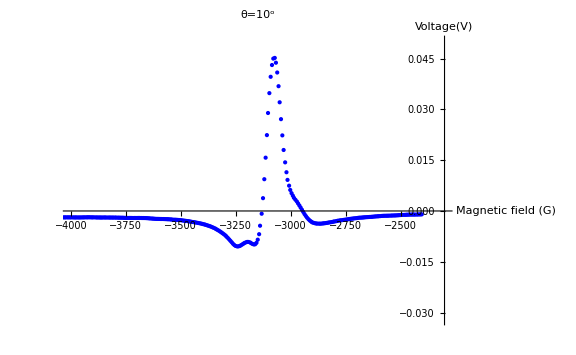

```mathematica
ten=Import["C:\\Users\\Peggy\\Desktop\\M2.6 ectron Spin Resonance\\EPRdata\\crystal\\10", "Table"];
a10=Take[ten, {5,285}];
pa1=ListPlot[a10,PlotRange->{{-4000,-2300}, {0.05,-0.032}} ,LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"θ=10^o" ,   AxesLabel->{"Magnetic field (G)", " Voltage(V)"}, PlotStyle->Directive[Thin,PointSize[Small],Blue]]
```

```mathematica
FindFit[a10, -(v*g (-a+x))/(π (g^2/4+(-a+x)^2)^2),{{a,-3200},{v,-3000},{g,150}},x]
```

{a→-3130.3,v→-741.871,g→155.646}

```mathematica
a1ten=NonlinearModelFit[a10, { -(v*g (-a+x))/(π (g^2/4+(-a+x)^2)^2),150<g<160, -1500<v<-300, -3200<a<-3000},{a,v,g } ,x ]
```

FittedModel[(36550.4 (3130.24+x))/((6029.48+(«19»+x)^2)^2)]

```mathematica
a1ten["AdjustedRSquared"]
```

0.697794

```mathematica
a1ten["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | -3130.18 | 1.75817 | -1780.36 | 0.
v | -735.476 | 57.6218 | -12.7639 | 1.12159×10^-29
g | 154.891 | 6.99073 | 22.1566 | 2.29723×10^-63

```mathematica
a1ten["BestFit"]
```

(36261.4 (3130.18+x))/((5997.8+(3130.18+x)^2)^2)

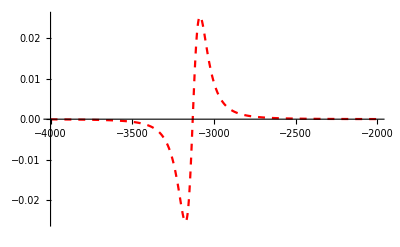

```mathematica
fita1=Plot[(36261.421320387184 (3130.1760543164555+x))/((5997.797597636244+(3130.1760543164555+x)^2)^2),{x,-4000,-2000}, PlotStyle->{Red, Dashed}, PlotRange->{ {0.047,-0.032}}]
```

```mathematica
Solve[D[(36261.421320387184 (3130.1760543164555+x))/((5997.797597636244+(3130.1760543164555+x)^2)^2),x]==0,x]
```

{{x→-3174.89},{x→-3085.46}}

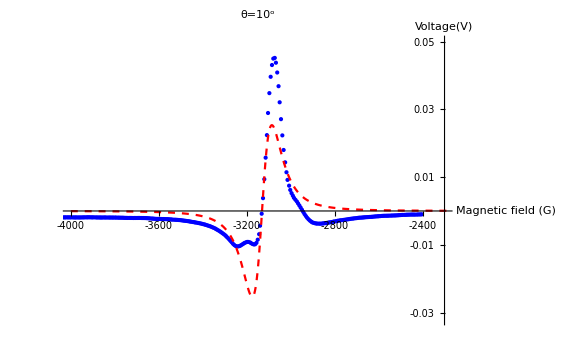

```mathematica
plo=Show[pa1,  fita1, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio,Ticks-> {{-4000,-3800,-3600,-3400,-3200,-3000,-2800,-2600,-2400},{-0.03,-0.01,0.01,0.03,0.05}}]
```

```mathematica
(*gaussian*)




gauss=Exp[-(-a+x)^2  /(2 *s^2)]/Sqrt[2*Pi*s^2]
```

(ⅇ^(-(-a+x)^2/(2 s^2)))/(√(2 π) √(s^2))

```mathematica
D[gauss, x]
```

-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))

```mathematica
FindFit[a10,-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,{{a,-3140},{v,-500},{s,50 }},x]
```

{a→-3136.74,v→-387.727,s→60.7857}

```mathematica
a2ten=NonlinearModelFit[a10, {-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,55<s<65, -490<v<0.4},{{a,-3140},v,s} ,x ]
```

FittedModel[0.000689271 ⅇ^(-0.0001355 (3136.71+x)^2) (3136.71+x)]

```mathematica
a2ten["AdjustedRSquared"]
```

0.709276

```mathematica
a2ten["ParameterTable"]

a2ten["BestFit"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-1281.82] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3136.71 | 1.89125 | -1658.54 | 0.
v | -387.281 | 23.3711 | -16.571 | 2.27659×10^-43
s | 60.7457 | 1.89469 | 32.061 | 2.19504×10^-95

0.000689271 ⅇ^(-0.0001355 (3136.71+x)^2) (3136.71+x)

```mathematica
FindMinimum[0.000689271390457476 ⅇ^(-0.00013550001002238254 (3136.71235996259+x)^2) (3136.71235996259+x),{x,-3180}]
```

{-0.0253956,{x→-3197.46}}

```mathematica
FindMaximum[0.000689271390457476 ⅇ^(-0.00013550001002238254 (3136.71235996259+x)^2) (3136.71235996259+x),{x,-3080}]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.0253956,{x→-3075.97}}

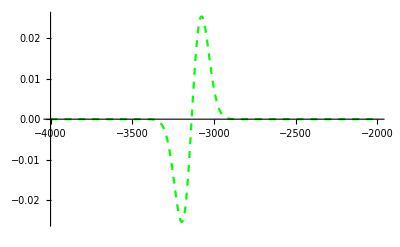

```mathematica
fita2=Plot[0.000689271390457476 ⅇ^(-0.00013550001002238254 (3136.71235996259+x)^2) (3136.71235996259+x),{x,-4000,-2000}, PlotStyle->{Green, Dashed}, PlotRange->{ {0.047,-0.032}}]
```

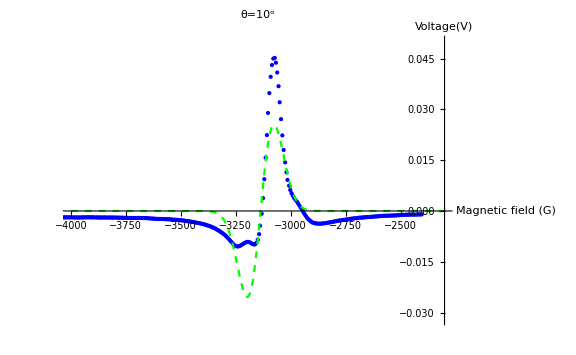

```mathematica
pg=Show[pa1,  fita2, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

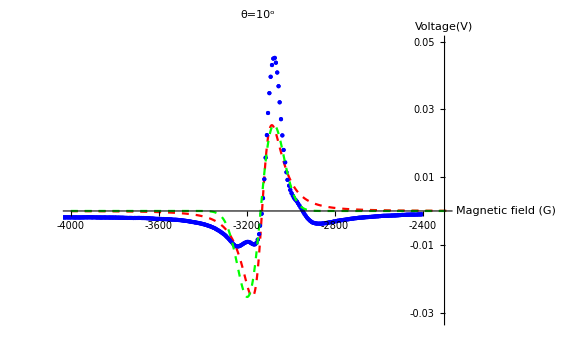

```mathematica
Show[plo,pg]
```

```mathematica
20 Degrees
```

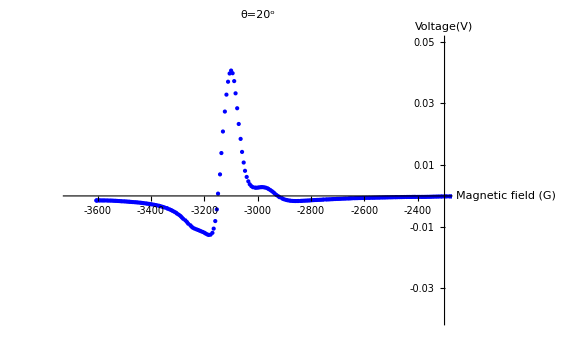

```mathematica
ClearAll["Global`*"]

twenty=Import["C:\\Users\\Peggy\\Desktop\\M2.6 ectron Spin Resonance\\EPRdata\\crystal\\20", "Table"];
a20=Take[twenty, {5,252}];
pa2=ListPlot[a20,PlotRange->{{-3700,-2300}, {0.05,-0.04}} ,LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"θ=20^o" ,   AxesLabel->{"Magnetic field (G)", " Voltage(V)"}, PlotStyle->Directive[Thin,PointSize[Small],Blue],Ticks-> {{-3600,-3400,-3200,-3000,-2800,-2600,-2400},{-0.03,-0.01,0.01,0.03,0.05}}]
```

```mathematica
FindFit[a20,  -(v*g (-a+x))/(π (g^2/4+(-a+x)^2)^2),{{a,-3190},g,v},x]
```

{a→-3147.5,g→133.943,v→-544.927}

```mathematica
a1ten=NonlinearModelFit[a20, { -(v*g (-a+x))/(π (g^2/4+(-a+x)^2)^2),100<g<150, -6000<v<-3, -3200<a<-3100},{a,v,g } ,x ]


a1ten["AdjustedRSquared"]

a1ten["ParameterTable"]

a1ten["BestFit"]
```

FittedModel[(23200.6 (3147.49+x))/((4480.14+(«18»+x)^2)^2)]

0.804516

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-1257.56] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3147.49 | 1.20082 | -2621.12 | 0.
v | -544.468 | 34.0846 | -15.974 | 7.62791×10^-40
g | 133.868 | 4.86271 | 27.5294 | 6.13111×10^-77

(23200.6 (3147.49+x))/((4480.14+(3147.49+x)^2)^2)

```mathematica
Solve[D[(23200.559645079302 (3147.492807593544+x))/((4480.137701096172+(3147.492807593544+x)^2)^2),x]==0,x]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→-3186.14},{x→-3108.85}}

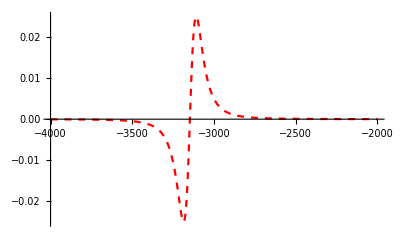

```mathematica
fita20a=Plot[(23200.559645079302 (3147.492807593544+x))/((4480.137701096172+(3147.492807593544+x)^2)^2),{x,-4000,-2000}, PlotStyle->{Red, Dashed}, PlotRange->{ {0.047,-0.032}}]
```

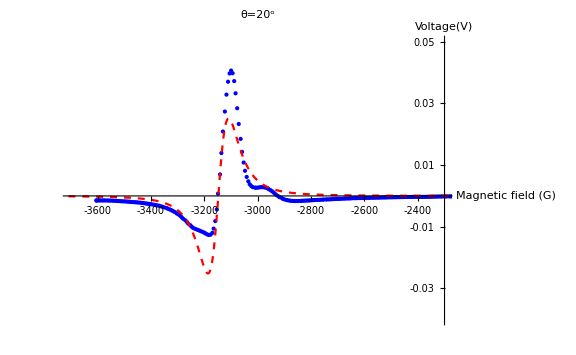

```mathematica
pl20=Show[pa2,  fita20a, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

```mathematica
(*gaussian*)


FindFit[a20 ,-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,{{a,-3150},{v,-900},{s,90}},x]
```

{a→-3150.69,v→-259.961,s→49.6749}

```mathematica
a2twe=NonlinearModelFit[a20, {-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,45<s<55, -290<v<0.4},{{a,-3150},v,s} ,x ]


a2twe["AdjustedRSquared"]


a2twe["ParameterTable"]

a2twe["BestFit"]
```

FittedModel[0.000846349 ⅇ^(-0.000202771 (3150.68+x)^2) (3150.68+x)]

0.797088

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-1238.74] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3150.68 | 1.29804 | -2427.27 | 0.
v | -259.767 | 13.1787 | -19.7111 | 1.85627×10^-52
s | 49.6571 | 1.30406 | 38.079 | 6.91546×10^-105

0.000846349 ⅇ^(-0.000202771 (3150.68+x)^2) (3150.68+x)

```mathematica
FindMinimum[0.0008463488818434502 ⅇ^(-0.0002027714274558405 (3150.684939178581+x)^2) (3150.684939178581+x),{x,-3190}]



FindMaximum[0.0008463488818434502 ⅇ^(-0.0002027714274558405 (3150.684939178581+x)^2) (3150.684939178581+x),{x,-3110}]
```

{-0.0254908,{x→-3200.34}}

{0.0254908,{x→-3101.03}}

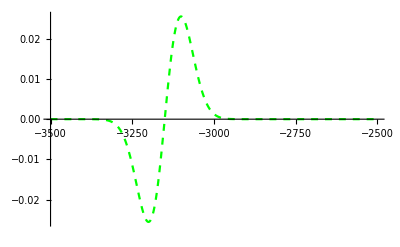

```mathematica
fita20b=Plot[0.0008463488818434502 ⅇ^(-0.0002027714274558405 (3150.684939178581+x)^2) (3150.684939178581+x),{x,-3500,-2500}, PlotStyle->{Green, Dashed}, PlotRange->{ {0.03,-0.032}}]
```

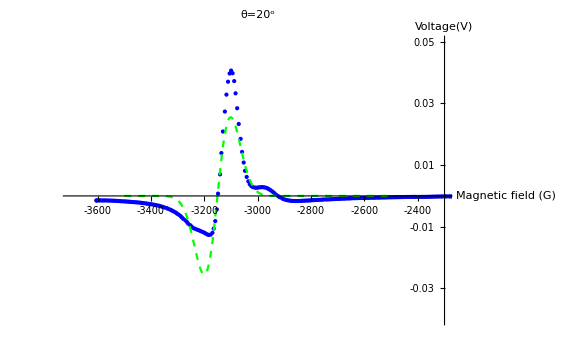

```mathematica
pg20=Show[pa2,  fita20b, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

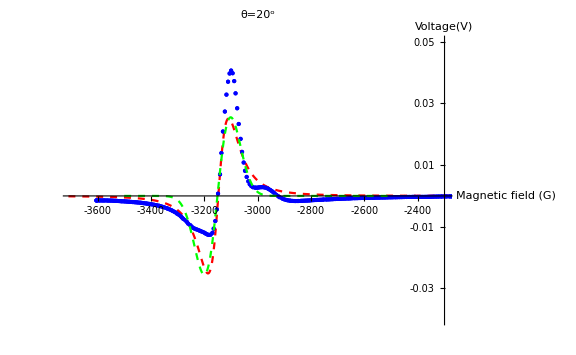

```mathematica
Show[pl20, pg20]
```

```mathematica
30 Degrees
```

```mathematica
ClearAll["Global`*"]
```

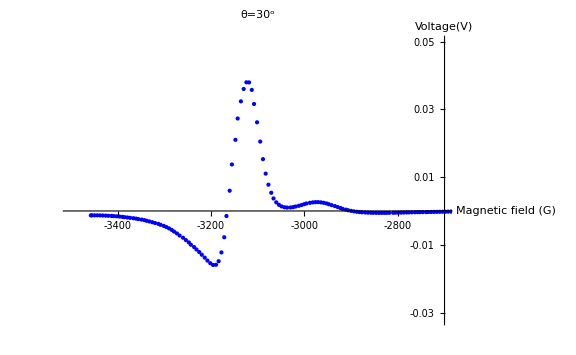

```mathematica
therty=Import["C:\\Users\\Peggy\\Desktop\\M2.6 ectron Spin Resonance\\EPRdata\\crystal\\30", "Table"];
a30=Take[therty, {5,139}];
pa3=ListPlot[a30,PlotRange->{{-3500,-2700}, {0.05,-0.032}} ,LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"θ=30^o" ,   AxesLabel->{"Magnetic field (G)", " Voltage(V)"}, PlotStyle->Directive[Thin,PointSize[Small],Blue], Ticks-> {{-3600,-3400,-3200,-3000,-2800,-2600,-2400},{-0.03,-0.01,0.01,0.03,0.05}}]
```

```mathematica
FindFit[a30, -(v*g (-a+x))/(π (g^2/4+(-a+x)^2)^2),{{a,-3200},g,v},x]
```

{a→-3163.38,g→-110.187,v→379.297}

```mathematica
a1the=NonlinearModelFit[a30, { -(v*g (-a+x))/(π (g^2/4+(-a+x)^2)^2),90<g<150, -900<v<-10,-3180<a<-3100},{a,v,g } ,x ]


a1the["AdjustedRSquared"]

a1the["ParameterTable"]

a1the["BestFit"]
```

FittedModel[(13303.8 (3163.38+x))/((3035.38+(«19»+x)^2)^2)]

0.857213

| Estimate | Standard Error | t-Statistic | P-Value
a | -3163.38 | 1.10821 | -2854.5 | 4.65823×10^-318
v | -379.306 | 26.5304 | -14.2971 | 1.35467×10^-28
g | 110.189 | 4.46602 | 24.6726 | 2.77144×10^-51

(13303.8 (3163.38+x))/((3035.38+(3163.38+x)^2)^2)

```mathematica
Solve[D[(13303.828675366389 (3163.3781243499025+x))/((3035.3834918862362+(3163.3781243499025+x)^2)^2),x]==0,x]
```

{{x→-3195.19},{x→-3131.57}}

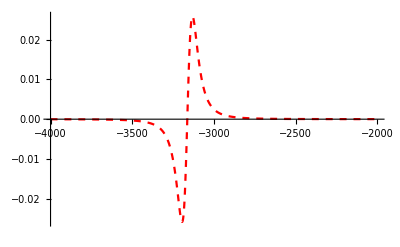

```mathematica
fita30a=Plot[(13303.828675366389 (3163.3781243499025+x))/((3035.3834918862362+(3163.3781243499025+x)^2)^2),{x,-4000,-2000}, PlotStyle->{Red, Dashed}, PlotRange->{ {0.047,-0.032}}]
```

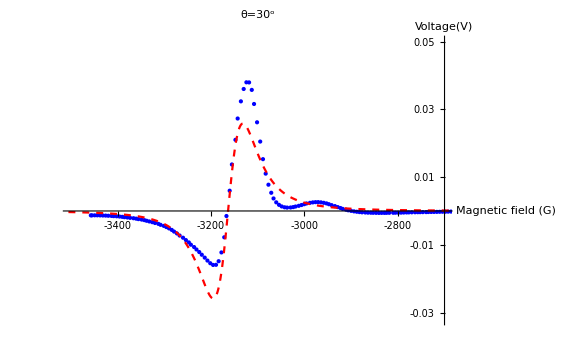

```mathematica
pl30=Show[pa3,  fita30a, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

```mathematica
(*gaussian*)


FindFit[a30 ,-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,{{a,-3170},{v,-900},{s,20}},x]
```

{a→-3164.55,v→-173.984,s→39.7329}

```mathematica
a2the=NonlinearModelFit[a30, {-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,30<s<40, -190<v<-124},{{a,-3150},v,s} ,x ]


a2the["AdjustedRSquared"]


a2the["ParameterTable"]

a2the["BestFit"]
```

FittedModel[0.00111134 ⅇ^(-0.000318564 (3164.5+x)^2) (3164.5+x)]

0.853931

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-726.357] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3164.5 | 1.14554 | -2762.46 | 3.52438×10^-316
v | -173.219 | 9.70029 | -17.8571 | 5.06837×10^-37
s | 39.6175 | 1.1507 | 34.4289 | 8.3366×10^-68

0.00111134 ⅇ^(-0.000318564 (3164.5+x)^2) (3164.5+x)

```mathematica
FindMinimum[0.0011113364393775733 ⅇ^(-0.0003185640870531835 (3164.500415127496+x)^2) (3164.500415127496+x),{x,-3200}]


FindMaximum[0.0011113364393775733 ⅇ^(-0.0003185640870531835 (3164.500415127496+x)^2) (3164.500415127496+x),{x,-3110}]
```

{-0.0267045,{x→-3204.12}}

{0.0267045,{x→-3124.88}}

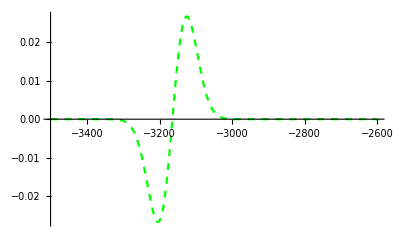

```mathematica
fita30b=Plot[0.0011113364393775733 ⅇ^(-0.0003185640870531835 (3164.500415127496+x)^2) (3164.500415127496+x),{x,-3500,-2600}, PlotStyle->{Green, Dashed}, PlotRange->{ {0.047,-0.032}}]
```

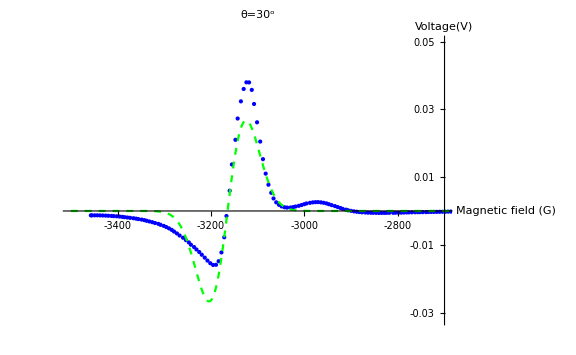

```mathematica
pg30=Show[pa3,  fita30b, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

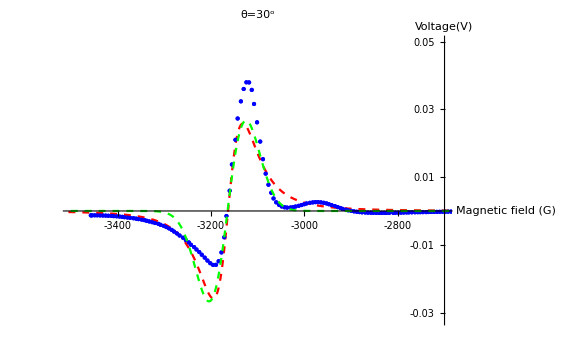

```mathematica
Show[pl30, pg30]
```

```mathematica
(*here gaussian is better*)
```

```mathematica
40 Degrees
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
forty=Import["C:\\Users\\Peggy\\Desktop\\M2.6 ectron Spin Resonance\\EPRdata\\crystal\\40", "Table"];
```

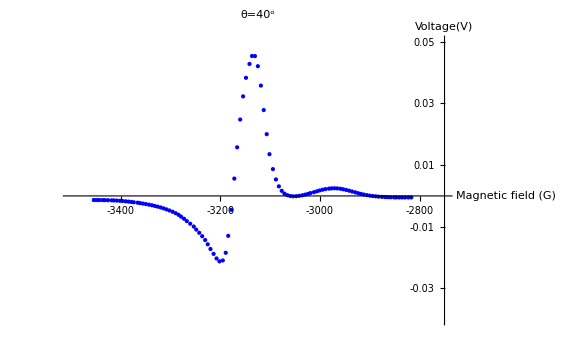

```mathematica
a40=Take[forty, {5,114}];
pa4=ListPlot[a40,PlotRange->{{-3500,-2750}, {0.05,-0.04}} ,LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"θ=40^o" ,   AxesLabel->{"Magnetic field (G)", " Voltage(V)"}, PlotStyle->Directive[Thin,PointSize[Small],Blue], Ticks-> {{-3600,-3400,-3200,-3000,-2800},{-0.03,-0.01,0.01,0.03,0.05}}]
```

```mathematica
FindFit[a40,  -(v*g (-a+x))/(π (g^2/4+(-a+x)^2)^2),{{a,-3200},g,v},x]
```

{a→-3173.07,g→-97.6192,v→366.106}

```mathematica
a1forty=NonlinearModelFit[a40, { -(v*g (-a+x))/(π (g^2/4+(-a+x)^2)^2),90<g<100, -500<v<-300,-3190<a<-3160},{a,v,g } ,x ]


a1forty["AdjustedRSquared"]

a1forty["ParameterTable"]

a1forty["BestFit"]
```

FittedModel[(11359.8 (3173.06+x))/((2379.61+(«19»+x)^2)^2)]

0.859364

| Estimate | Standard Error | t-Statistic | P-Value
a | -3173.06 | 1.07844 | -2942.27 | 2.03681×10^-264
v | -365.794 | 28.0528 | -13.0395 | 7.70613×10^-24
g | 97.5625 | 4.32946 | 22.5346 | 2.00178×10^-42

(11359.8 (3173.06+x))/((2379.61+(3173.06+x)^2)^2)

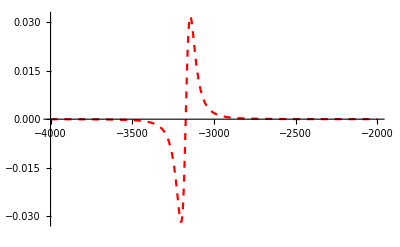

```mathematica
fita40a=Plot[(11359.752620608795 (3173.0631541157004+x))/((2379.607977202945+(3173.0631541157004+x)^2)^2),{x,-4000,-2000}, PlotStyle->{Red, Dashed}, PlotRange->{ {0.047,-0.032}}]
```

```mathematica
Solve[D[(11359.752620608795 (3173.0631541157004+x))/((2379.607977202945+(3173.0631541157004+x)^2)^2),x]==0,x]
```

{{x→-3201.23},{x→-3144.9}}

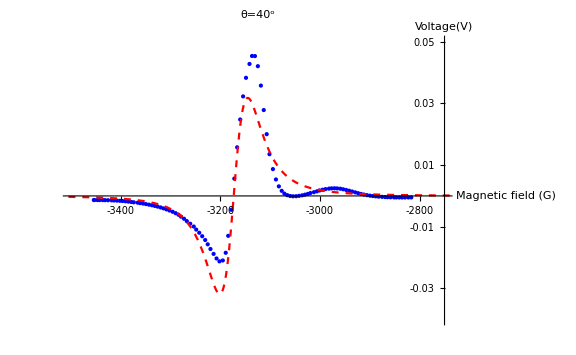

```mathematica
pl40=Show[pa4,  fita40a, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

```mathematica
(*gaussian*)


FindFit[a40 ,-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,{{a,-3180},{v,-300},{s,35}},x]
```

{a→-3173.65,v→-168.686,s→35.1777}

```mathematica
a2for=NonlinearModelFit[a40, {-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,30<s<40, -190<v<-154},{{a,-3170},v,s} ,x ]


a2for["AdjustedRSquared"]


a2for["ParameterTable"]

a2for["BestFit"]
```

FittedModel[0.00154589 ⅇ^(-0.000404023 (3173.66+x)^2) (3173.66+x)]

0.8666

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3173.66 | 1.06926 | -2968.09 | 7.99862×10^-265
v | -168.7 | 9.94861 | -16.9571 | 4.30938×10^-32
s | 35.1789 | 1.07801 | 32.633 | 1.96211×10^-57

0.00154589 ⅇ^(-0.000404023 (3173.66+x)^2) (3173.66+x)

```mathematica
FindMinimum[0.001545887827308254 ⅇ^(-0.0004040226214260055 (3173.6550182407873+x)^2) (3173.6550182407873+x),{x,-3190}]


FindMaximum[0.001545887827308254 ⅇ^(-0.0004040226214260055 (3173.6550182407873+x)^2) (3173.6550182407873+x),{x,-3150}]
```

{-0.0329847,{x→-3208.83}}

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.0329847,{x→-3138.48}}

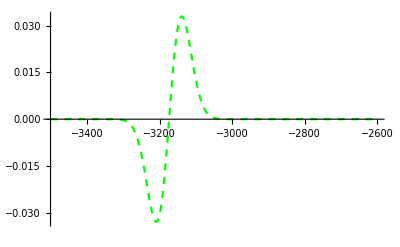

```mathematica
fita40b=Plot[0.001545887827308254 ⅇ^(-0.0004040226214260055 (3173.6550182407873+x)^2) (3173.6550182407873+x),{x,-3500,-2600}, PlotStyle->{Green, Dashed}, PlotRange->{ {0.047,-0.042}}]
```

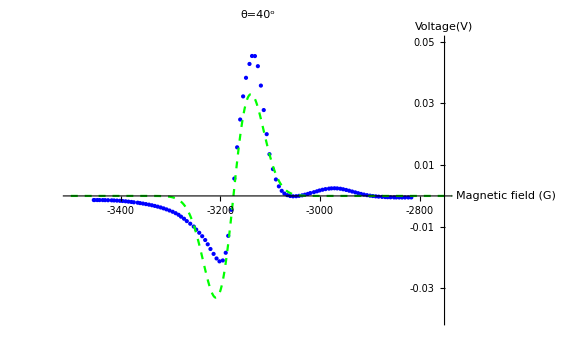

```mathematica
pg40=Show[pa4,  fita40b, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

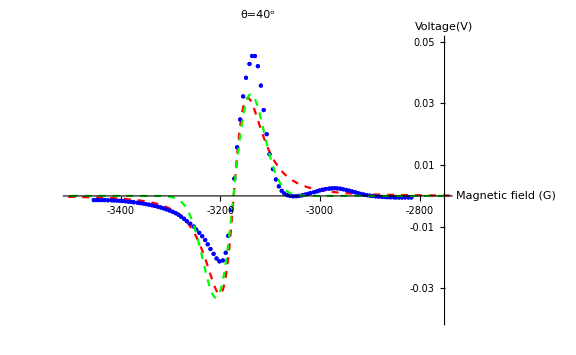

```mathematica
Show[pl40, pg40]
```

```mathematica
(*here gaussian is better*)
```

```mathematica
50 Degrees
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
fifty=Import["C:\\Users\\Peggy\\Desktop\\M2.6 ectron Spin Resonance\\EPRdata\\crystal\\50", "Table"];
```

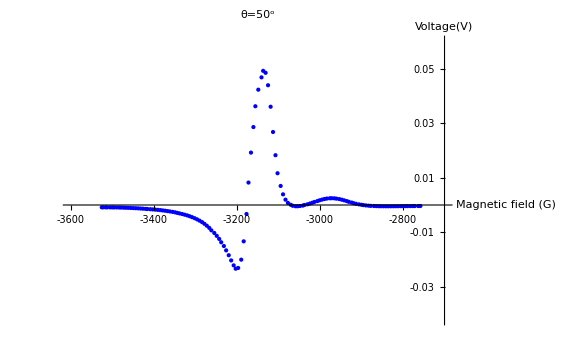

```mathematica
a50=Take[fifty, {5,136}];
pa5=ListPlot[a50,PlotRange->{{-3600,-2700}, {0.06,-0.042}} ,LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"θ=50^o" ,   AxesLabel->{"Magnetic field (G)", " Voltage(V)"}, PlotStyle->Directive[Thin,PointSize[Small],Blue], Ticks-> {{-3600,-3400,-3200,-3000,-2800,-2600,-2400},{-0.03,-0.01,0.01,0.03,0.05}}]
```

```mathematica
FindFit[a50,  -(v*g (-a+x))/(π (g^2/4+(-a+x)^2)^2),{{a,-3250},g,v},x]
```

{a→-3173.67,g→93.3076,v→-366.976}

```mathematica
a1fifty=NonlinearModelFit[a50, { -(v*g (-a+x))/(π (g^2/4+(-a+x)^2)^2),90<g<100, -400<v<-300,-3190<a<-3100},{a,v,g } ,x ]


a1fifty["AdjustedRSquared"]

a1fifty["ParameterTable"]

a1fifty["BestFit"]
```

FittedModel[(10888.8 (3173.66+x))/((2175.22+(«19»+x)^2)^2)]

0.858854

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-738.167] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3173.66 | 0.933439 | -3399.97 | 2.62×10^-321
v | -366.73 | 25.6707 | -14.2859 | 2.38821×10^-28
g | 93.2785 | 3.81298 | 24.4634 | 2.7158×10^-50

(10888.8 (3173.66+x))/((2175.22+(3173.66+x)^2)^2)

```mathematica
Solve[D[(10888.752623882256 (3173.6634623894465+x))/((2175.218573310336+(3173.6634623894465+x)^2)^2),x]==0,x]
```

{{x→-3200.59},{x→-3146.74}}

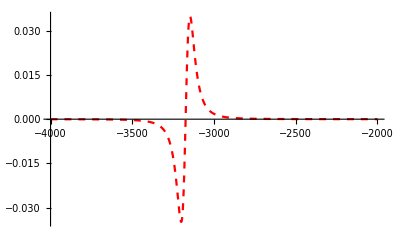

```mathematica
fita50a=Plot[(10888.752623882256 (3173.6634623894465+x))/((2175.218573310336+(3173.6634623894465+x)^2)^2),{x,-4000,-2000}, PlotStyle->{Red, Dashed}, PlotRange->{ {0.047,-0.042}}]
```

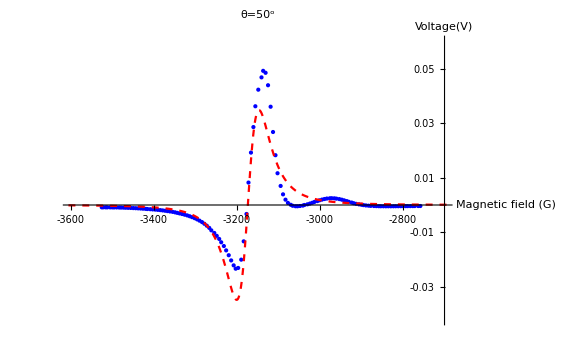

```mathematica
pl50=Show[pa5,  fita50a, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

```mathematica
(*gaussian*)


FindFit[a50 ,-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,{{a,-3170},{v,-300},{s,30}},x]
```

{a→-3174.44,v→-171.627,s→33.9981}

```mathematica
a2fif=NonlinearModelFit[a50, {-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,30<s<35, -190<v<-4},{{a,-3180},v,s} ,x ]


a2fif["AdjustedRSquared"]


a2fif["ParameterTable"]

a2fif["BestFit"]
```

FittedModel[0.00174488 ⅇ^(-0.000433582 (3174.43+x)^2) (3174.43+x)]

0.867628

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-737.457] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3174.43 | 0.938811 | -3381.33 | 5.326×10^-321
v | -171.278 | 9.16281 | -18.6928 | 1.57807×10^-38
s | 33.9586 | 0.946995 | 35.8593 | 5.99313×10^-69

0.00174488 ⅇ^(-0.000433582 (3174.43+x)^2) (3174.43+x)

```mathematica
FindMinimum[0.0017448759774453208 ⅇ^(-0.00043358191693180695 (3174.4281300751736+x)^2) (3174.4281300751736+x),{x,-3200}]


FindMaximum[0.0017448759774453208 ⅇ^(-0.00043358191693180695 (3174.4281300751736+x)^2) (3174.4281300751736+x),{x,-3150}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{-0.0359391,{x→-3208.39}}

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.0359391,{x→-3140.47}}

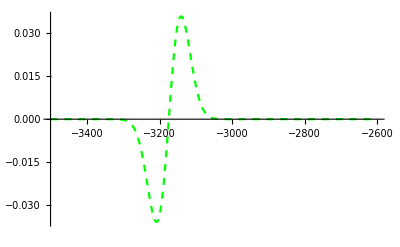

```mathematica
fita50b=Plot[0.0017448759774453208 ⅇ^(-0.00043358191693180695 (3174.4281300751736+x)^2) (3174.4281300751736+x),{x,-3500,-2600}, PlotStyle->{Green, Dashed}, PlotRange->{ {0.047,-0.042}}]
```

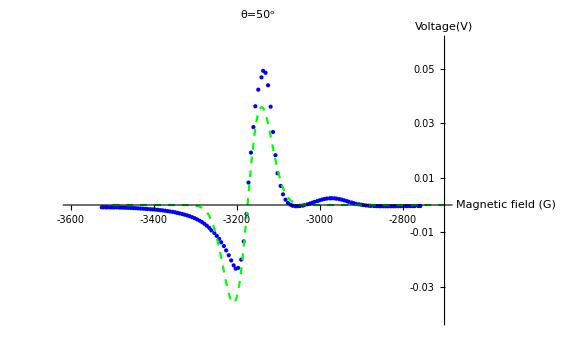

```mathematica
pg50=Show[pa5,  fita50b, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

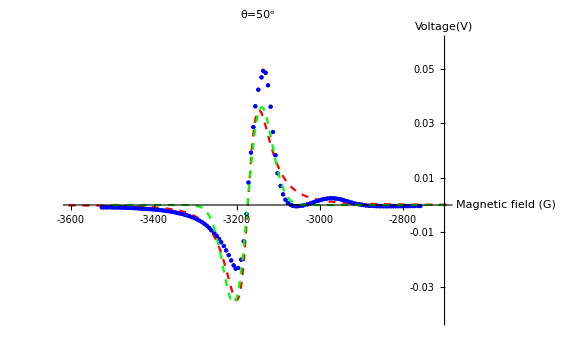

```mathematica
Show[pl50, pg50]
```

```mathematica
60 Degrees
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
sixty=Import["C:\\Users\\Peggy\\Desktop\\M2.6 ectron Spin Resonance\\EPRdata\\crystal\\60", "Table"];
```

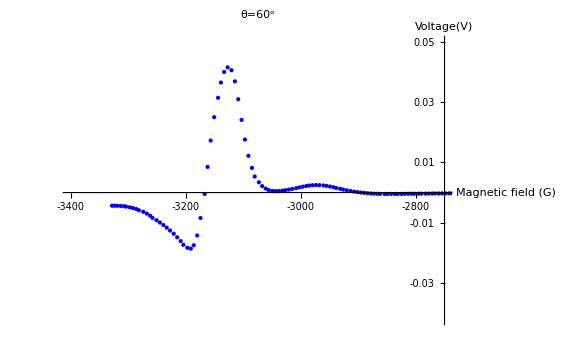

```mathematica
a60=Take[sixty, {5,145}];
pa6=ListPlot[a60,PlotRange->{{-3400,-2750}, {0.05,-0.042}} ,LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"θ=60^o" ,   AxesLabel->{"Magnetic field (G)", " Voltage(V)"}, PlotStyle->Directive[Thin,PointSize[Small],Blue], Ticks-> {{-3600,-3400,-3200,-3000,-2800,-2600,-2400},{-0.03,-0.01,0.01,0.03,0.05}}]
```

```mathematica
FindFit[a60,  -(v*g (-a+x))/(π (g^2/4+(-a+x)^2)^2),{{a,-3200},g,v},x]
```

{a→-3165.87,g→101.785,v→-356.986}

```mathematica
a1sixtz=NonlinearModelFit[a60, { -(v*g (-a+x))/(π (g^2/4+(-a+x)^2)^2),99<g<110, -400<v<-300,-3170<a<-3150},{a,v,g } ,x ]


a1sixtz["AdjustedRSquared"]

a1sixtz["ParameterTable"]

a1sixtz["BestFit"]
```

FittedModel[(11567.2 (3165.87+x))/((2590.33+(«18»+x)^2)^2)]

0.859286

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-774.95] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3165.87 | 1.00049 | -3164.33 | 0.
v | -357.003 | 24.4924 | -14.5761 | 1.02164×10^-29
g | 101.791 | 4.01893 | 25.3278 | 9.75792×10^-54

(11567.2 (3165.87+x))/((2590.33+(3165.87+x)^2)^2)

```mathematica
Solve[D[(11567.23755957166 (3165.869513683232+x))/((2590.329582249262+(3165.869513683232+x)^2)^2),x]==0,x]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→-3195.25},{x→-3136.49}}

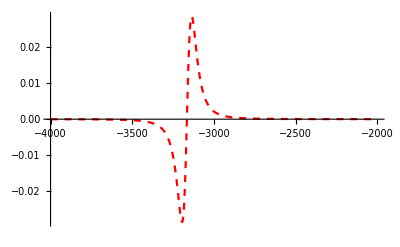

```mathematica
fita60a=Plot[(11567.23755957166 (3165.869513683232+x))/((2590.329582249262+(3165.869513683232+x)^2)^2),{x,-4000,-2000}, PlotStyle->{Red, Dashed}, PlotRange->{ {0.047,-0.042}}]
```

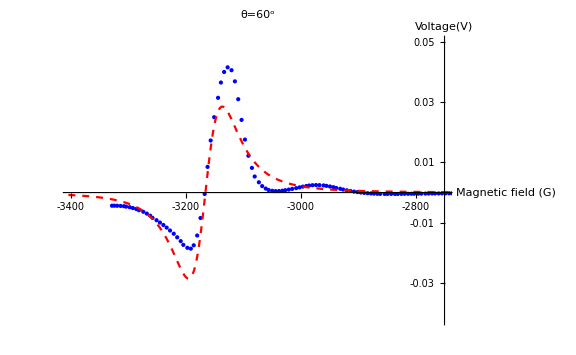

```mathematica
pl60=Show[pa6,  fita60a, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

```mathematica
(*gaussian*)


FindFit[a60 ,-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,{{a,-3170},{v,-300},{s,25}},x]
```

{a→-3166.99,v→-166.258,s→36.9739}

```mathematica
a2six=NonlinearModelFit[a60, {-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,30<s<40, -170<v<-160},{{a,-3170},v,s} ,x ]


a2six["AdjustedRSquared"]


a2six["ParameterTable"]

a2six["BestFit"]
```

FittedModel[0.00131347 ⅇ^(-0.000366498 (3166.97+x)^2) (3166.97+x)]

0.86107

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-772.477] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3166.97 | 1.01893 | -3108.14 | 0.
v | -165.904 | 8.87707 | -18.689 | 1.25109×10^-39
s | 36.9359 | 1.01673 | 36.3282 | 1.62294×10^-72

0.00131347 ⅇ^(-0.000366498 (3166.97+x)^2) (3166.97+x)

```mathematica
FindMinimum[0.0013134675881986597 ⅇ^(-0.00036649844536346577 (3166.973825418895+x)^2) (3166.973825418895+x),{x,-3200}]


FindMaximum[0.0013134675881986597 ⅇ^(-0.00036649844536346577 (3166.973825418895+x)^2) (3166.973825418895+x),{x,-3150}]
```

{-0.0294253,{x→-3203.91}}

{0.0294253,{x→-3130.04}}

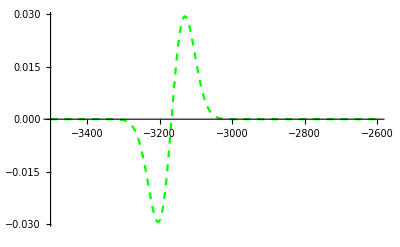

```mathematica
fita60b=Plot[0.0013134675881986597 ⅇ^(-0.00036649844536346577 (3166.973825418895+x)^2) (3166.973825418895+x),{x,-3500,-2600}, PlotStyle->{Green, Dashed}, PlotRange->{ {0.047,-0.042}}]
```

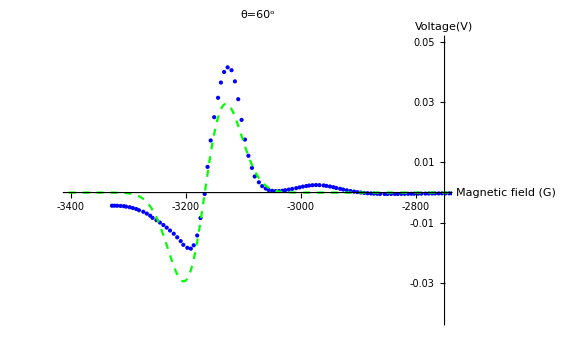

```mathematica
pg60=Show[pa6,  fita60b, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

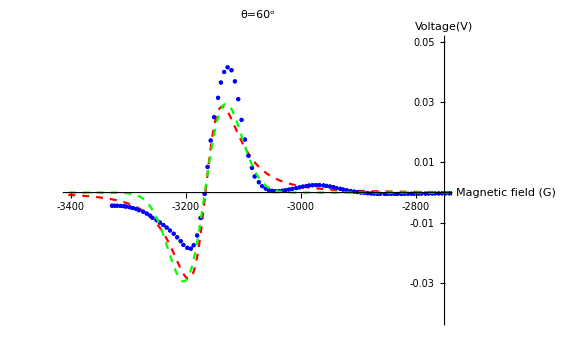

```mathematica
Show[pl60, pg60]
```

```mathematica
70 Degrees
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
seventy=Import["C:\\Users\\Peggy\\Desktop\\M2.6 ectron Spin Resonance\\EPRdata\\crystal\\70", "Table"];
```

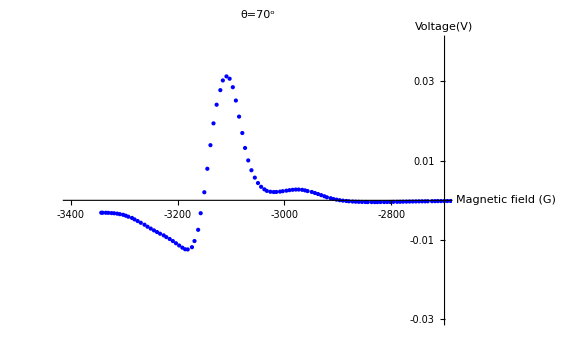

```mathematica
a70=Take[seventy, {5,129}];
pa7=ListPlot[a70,PlotRange->{{-3400,-2700}, {0.04,-0.03}} ,LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"θ=70^o" ,   AxesLabel->{"Magnetic field (G)", " Voltage(V)"}, PlotStyle->Directive[Thin,PointSize[Small],Blue], Ticks-> {{-3600,-3400,-3200,-3000,-2800,-2600,-2400},{-0.03,-0.01,0.01,0.03,0.05}}]
```

```mathematica
FindFit[a70, -(v*g (-a+x))/(π (g^2/4+(-a+x)^2)^2),{{a,-3190},g,v},x]
```

{a→-3151.03,g→-119.74,v→359.637}

```mathematica
a1seven=NonlinearModelFit[a70, { -(v*g (-a+x))/(π (g^2/4+(-a+x)^2)^2),110<g<130, -400<v<-300},{{a,-3151},v,g } ,x ]


a1seven["AdjustedRSquared"]

a1seven["ParameterTable"]

a1seven["BestFit"]
```

FittedModel[(13697.3 (3151.03+x))/((3582.62+(«19»+x)^2)^2)]

0.855717

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3151.03 | 1.26485 | -2491.24 | 5.79037×10^-289
v | -359.464 | 26.483 | -13.5734 | 3.83994×10^-26
g | 119.71 | 5.09879 | 23.4781 | 4.47504×10^-47

(13697.3 (3151.03+x))/((3582.62+(3151.03+x)^2)^2)

```mathematica
Solve[D[(13697.323781709023 (3151.0271001561573+x))/((3582.6162991476544+(3151.0271001561573+x)^2)^2),x]==0,x]
```

{{x→-3185.58},{x→-3116.47}}

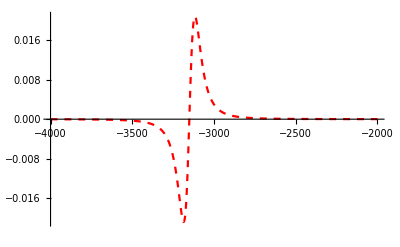

```mathematica
fita70a=Plot[(13697.323781709023 (3151.0271001561573+x))/((3582.6162991476544+(3151.0271001561573+x)^2)^2),{x,-4000,-2000}, PlotStyle->{Red, Dashed}, PlotRange->{ {0.047,-0.042}}]
```

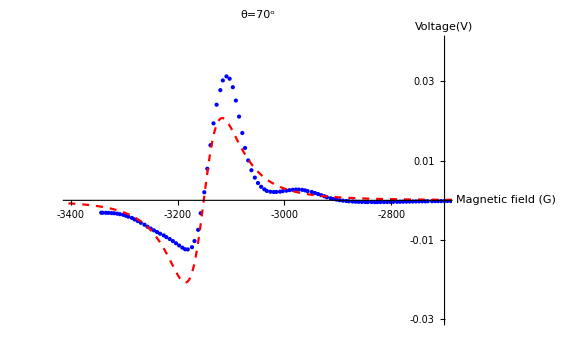

```mathematica
pl70=Show[pa7,  fita70a, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

```mathematica
(*gaussian*)


FindFit[a70 ,-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,{{a,-3160},{v,-200},{s,38}},x]
```

{a→-3153.02,v→-166.684,s→43.6858}

```mathematica
a2sev=NonlinearModelFit[a70, {-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,40<s<50, -170<v<-140},{{a,-3160},v,s} ,x ]


a2sev["AdjustedRSquared"]


a2sev["ParameterTable"]

a2sev["BestFit"]
```

FittedModel[0.000799699 ⅇ^(-0.000263582 (3152.96+x)^2) (3152.96+x)]

0.840473

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3152.96 | 1.38662 | -2273.85 | 3.98298×10^-284
v | -165.614 | 10.2057 | -16.2276 | 2.95592×10^-32
s | 43.5539 | 1.38738 | 31.3928 | 2.78945×10^-60

0.000799699 ⅇ^(-0.000263582 (3152.96+x)^2) (3152.96+x)

```mathematica
FindMinimum[0.0007996987457693233 ⅇ^(-0.0002635818552419851 (3152.9592709721655+x)^2) (3152.9592709721655+x),{x,-3190}]


FindMaximum[0.0007996987457693233 ⅇ^(-0.0002635818552419851 (3152.9592709721655+x)^2) (3152.9592709721655+x),{x,-3115}]
```

{-0.0211255,{x→-3196.51}}

{0.0211255,{x→-3109.41}}

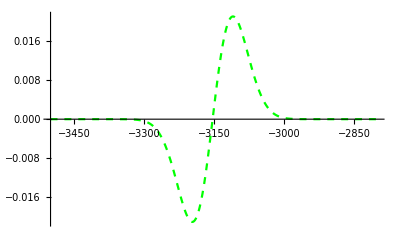

```mathematica
fita70b=Plot[0.0007996987457693233 ⅇ^(-0.0002635818552419851 (3152.9592709721655+x)^2) (3152.9592709721655+x),{x,-3500,-2800}, PlotStyle->{Green, Dashed}, PlotRange->{ {0.047,-0.042}}]
```

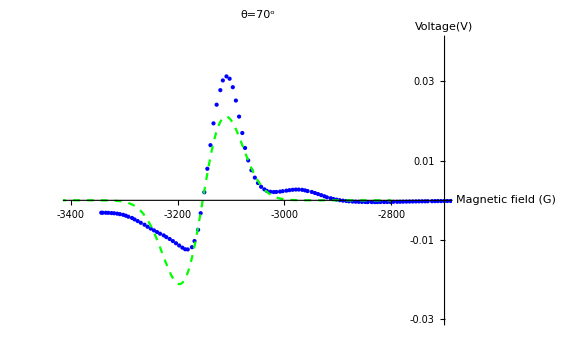

```mathematica
pg70=Show[pa7,  fita70b, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

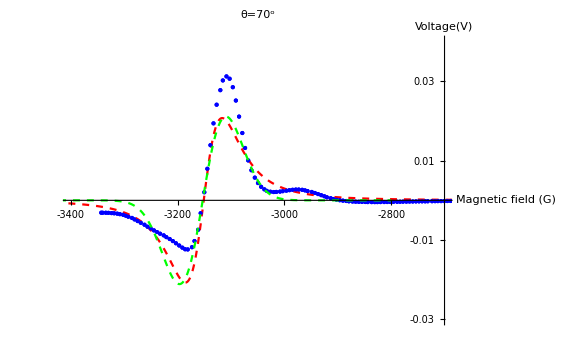

```mathematica
Show[pl70, pg70]
```

```mathematica
80 Degrees
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
eighty=Import["C:\\Users\\Peggy\\Desktop\\M2.6 ectron Spin Resonance\\EPRdata\\crystal\\80", "Table"];
```

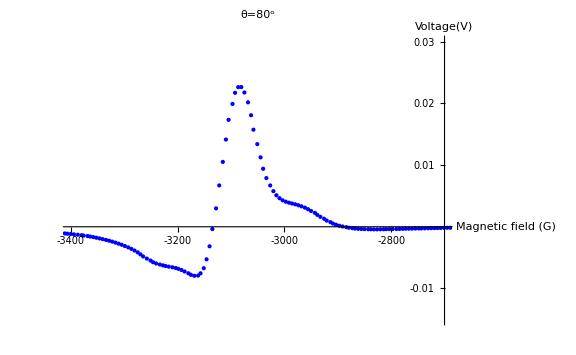

```mathematica
a80=Take[eighty, {5,166}];
pa8=ListPlot[a80,PlotRange->{{-3400,-2700}, {0.03,-0.015}} ,LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"θ=80^o" ,   AxesLabel->{"Magnetic field (G)", " Voltage(V)"}, PlotStyle->Directive[Thin,PointSize[Small],Blue], Ticks-> {{-3600,-3400,-3200,-3000,-2800,-2600,-2400},{-0.03,-0.01,0.01,0.02,0.03}}]
```

```mathematica
FindFit[a80,  -(v*g (-a+x))/(π (g^2/4+(-a+x)^2)^2),{{a,-3200},g,v},x]
```

{a→-3132.61,g→148.719,v→-389.147}

```mathematica
a1eig=NonlinearModelFit[a80, { -(v*g (-a+x))/(π (g^2/4+(-a+x)^2)^2),140<g<155, -800<v<-200},{{a,-3140},v,g } ,x ]


a1eig["AdjustedRSquared"]

a1eig["ParameterTable"]

a1eig["BestFit"]
```

FittedModel[(18272.6 (3132.56+x))/((5493.53+(«19»+x)^2)^2)]

0.848465

| Estimate | Standard Error | t-Statistic | P-Value
a | -3132.56 | 1.42136 | -2203.91 | 0.
v | -387.252 | 25.7219 | -15.0553 | 2.0974×10^-32
g | 148.237 | 5.67113 | 26.1388 | 1.92475×10^-59

(18272.6 (3132.56+x))/((5493.53+(3132.56+x)^2)^2)

```mathematica
Solve[D[(18272.55211016772 (3132.5583581688875+x))/((5493.528005884518+(3132.5583581688875+x)^2)^2),x]==0,x]
```

{{x→-3175.35},{x→-3089.77}}

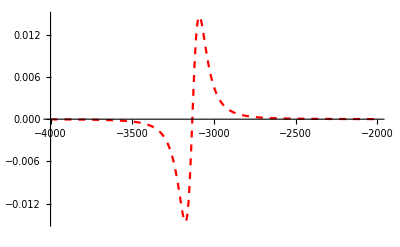

```mathematica
fita80a=Plot[(18272.55211016772 (3132.5583581688875+x))/((5493.528005884518+(3132.5583581688875+x)^2)^2),{x,-4000,-2000}, PlotStyle->{Red, Dashed}, PlotRange->{ {0.047,-0.042}}]
```

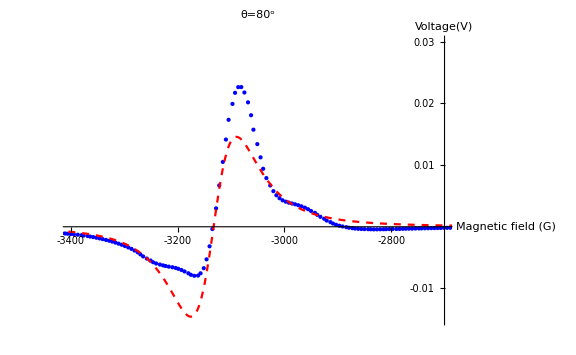

```mathematica
pl80=Show[pa8,  fita80a, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

```mathematica
(*gaussian*)


FindFit[a80 ,-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,{{a,-3140},{v,-300},{s,45}},x]
```

{a→-3136.01,v→-186.787,s→55.7215}

```mathematica
a2eig=NonlinearModelFit[a80, {-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,50<s<60 ,-190<v<-4},{{a,-3140},v,s} ,x ]


a2eig["AdjustedRSquared"]


a2eig["ParameterTable"]

a2eig["BestFit"]
```

FittedModel[0.000432591 ⅇ^(-0.000162484 (3135.91+x)^2) (3135.91+x)]

0.821567

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-799.494] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3135.91 | 1.65756 | -1891.88 | 0.
v | -185.1 | 10.7441 | -17.2281 | 3.38982×10^-38
s | 55.4727 | 1.66198 | 33.3775 | 1.01099×10^-73

0.000432591 ⅇ^(-0.000162484 (3135.91+x)^2) (3135.91+x)

```mathematica
FindMinimum[0.00043259103718272843 ⅇ^(-0.00016248408068279797 (3135.905771443873+x)^2) (3135.905771443873+x),{x,-3180}]

FindMaximum[0.00043259103718272843 ⅇ^(-0.00016248408068279797 (3135.905771443873+x)^2) (3135.905771443873+x),{x,-3090}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{-0.0145549,{x→-3191.38}}

{0.0145549,{x→-3080.43}}

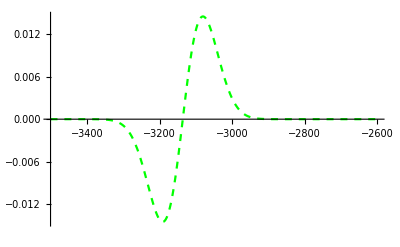

```mathematica
fita80b=Plot[0.00043259103718272843 ⅇ^(-0.00016248408068279797 (3135.905771443873+x)^2) (3135.905771443873+x),{x,-3500,-2600}, PlotStyle->{Green, Dashed}, PlotRange->{ {0.047,-0.042}}]
```

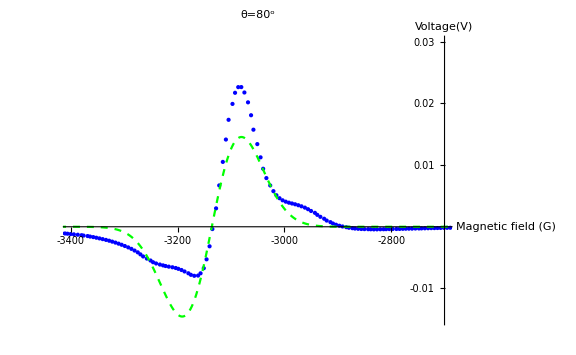

```mathematica
pg80=Show[pa8,  fita80b, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

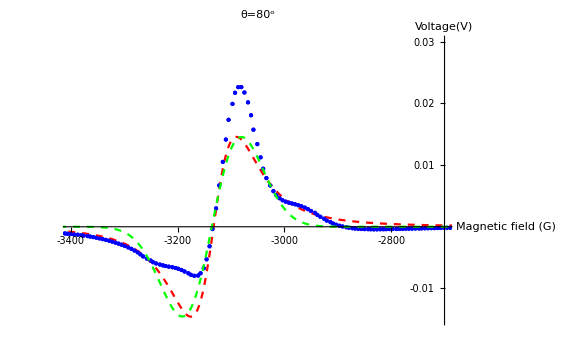

```mathematica
Show[pl80, pg80]
```

```mathematica
90 Degrees
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
ninty=Import["C:\\Users\\Peggy\\Desktop\\M2.6 ectron Spin Resonance\\EPRdata\\crystal\\90", "Table"];
```

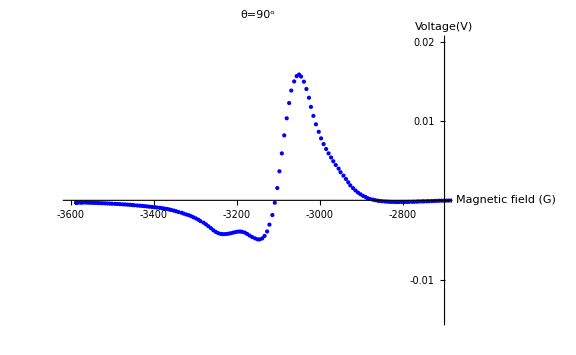

```mathematica
a90=Take[ninty, {5,216}];
pa9=ListPlot[a90,PlotRange->{{-3600,-2700}, {0.02,-0.015}} ,LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"θ=90^o" ,   AxesLabel->{"Magnetic field (G)", " Voltage(V)"}, PlotStyle->Directive[Thin,PointSize[Small],Blue], Ticks-> {{-3600,-3400,-3200,-3000,-2800,-2600,-2400},{-0.02,-0.01,0.01,0.02,0.05}}]
```

```mathematica
FindFit[a90, -(v*g (-a+x))/(π (g^2/4+(-a+x)^2)^2),{{a,-3110},g,v},x]
```

{a→-3107.19,g→-177.481,v→380.595}

```mathematica
a1nin=NonlinearModelFit[a90, { -(v*g (-a+x))/(π (g^2/4+(-a+x)^2)^2),170<g<180, -400<v<-300},{{a,-3140},v,g } ,x ]


a1nin["AdjustedRSquared"]

a1nin["ParameterTable"]

a1nin["BestFit"]
```

FittedModel[(20838.5 (3106.92+x))/((7682.21+(«19»+x)^2)^2)]

0.817484

| Estimate | Standard Error | t-Statistic | P-Value
a | -3106.92 | 1.63789 | -1896.9 | 0.
v | -373.459 | 24.1969 | -15.4342 | 2.25288×10^-36
g | 175.296 | 6.56099 | 26.718 | 2.48646×10^-69

(20838.5 (3106.92+x))/((7682.21+(3106.92+x)^2)^2)

```mathematica
Solve[D[(20838.49582292668 (3106.9224521284245+x))/((7682.205041015241+(3106.9224521284245+x)^2)^2),x]==0,x]
```

{{x→-3157.53},{x→-3056.32}}

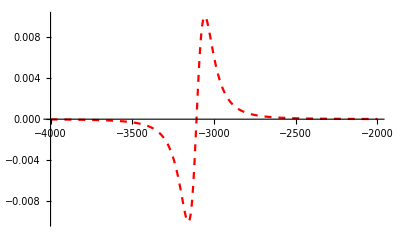

```mathematica
fita90a=Plot[(20838.49582292668 (3106.9224521284245+x))/((7682.205041015241+(3106.9224521284245+x)^2)^2),{x,-4000,-2000}, PlotStyle->{Red, Dashed}, PlotRange->{ {0.047,-0.042}}]
```

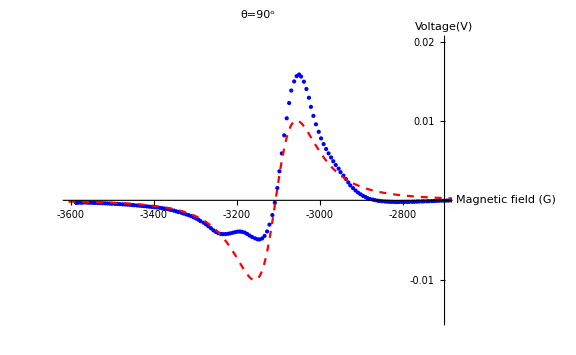

```mathematica
pl90=Show[pa9,  fita90a, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

```mathematica
(*gaussian*)


FindFit[a90 ,-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,{{a,-3110},{v,-200},{s,55}},x]
```

{a→-3113.16,v→-198.318,s→69.9904}

```mathematica
a2nin=NonlinearModelFit[a90, {-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,65<s<75,-200<v<-140},{{a,-3120},v,s} ,x ]


a2nin["AdjustedRSquared"]


a2nin["ParameterTable"]

a2nin["BestFit"]
```

FittedModel[0.0002337 ⅇ^(-0.000104831 (3112.71+x)^2) (3112.71+x)]

0.803669

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-988.462] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3112.71 | 1.92805 | -1614.44 | 0.
v | -192.959 | 10.4299 | -18.5006 | 6.70207×10^-46
s | 69.062 | 1.92906 | 35.8009 | 4.07149×10^-91

0.0002337 ⅇ^(-0.000104831 (3112.71+x)^2) (3112.71+x)

```mathematica
FindMinimum[0.00023369981760012795 ⅇ^(-0.00010483149092920644 (3112.710398286736+x)^2) (3112.710398286736+x),{x,-3100}]


FindMaximum[0.00023369981760012795 ⅇ^(-0.00010483149092920644 (3112.710398286736+x)^2) (3112.710398286736+x),{x,-3000}]
```

{-0.00978927,{x→-3181.77}}

{0.00978927,{x→-3043.65}}

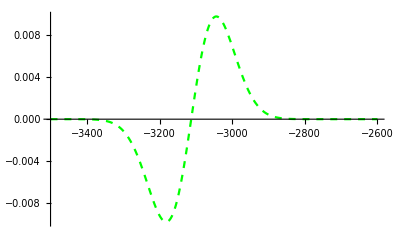

```mathematica
fita90b=Plot[0.00023369981760012795 ⅇ^(-0.00010483149092920644 (3112.710398286736+x)^2) (3112.710398286736+x),{x,-3500,-2600}, PlotStyle->{Green, Dashed}, PlotRange->{ {0.047,-0.042}}]
```

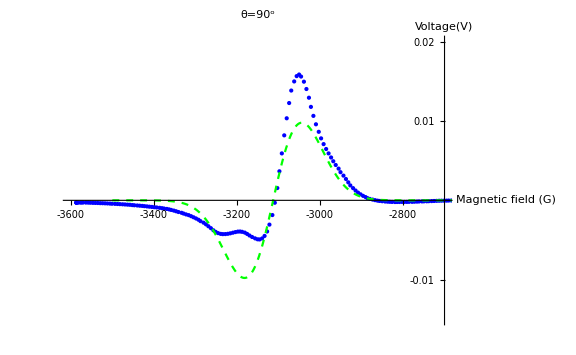

```mathematica
pg90=Show[pa9,  fita90b, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

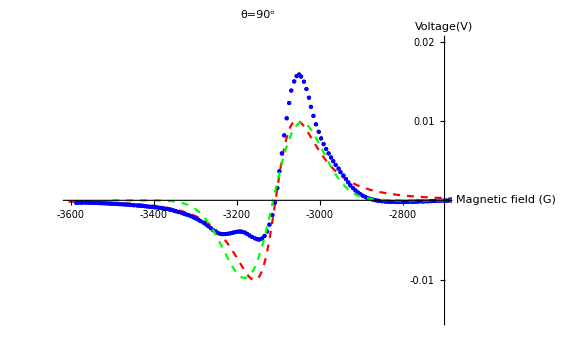

```mathematica
Show[pl90, pg90,ImageSize->Large, AspectRatio->1/GoldenRatio]
```

```mathematica
100 Degrees
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
hun=Import["C:\\Users\\Peggy\\Desktop\\M2.6 ectron Spin Resonance\\EPRdata\\crystal\\100", "Table"];
```

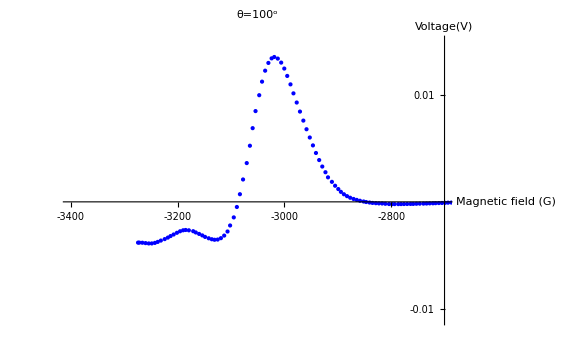

```mathematica
a100=Take[hun, {5,202}];
pa10=ListPlot[a100,PlotRange->{{-3400,-2700}, {0.015,-0.011}} ,LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"θ=100^o" ,   AxesLabel->{"Magnetic field (G)", " Voltage(V)"}, PlotStyle->Directive[Thin,PointSize[Small],Blue], Ticks-> {{-3600,-3400,-3200,-3000,-2800,-2600,-2400},{-0.03,-0.01,0.01,0.03,0.05}}]
```

```mathematica
FindFit[a100,  -(v*g (-a+x))/(π (g^2/4+(-a+x)^2)^2),{{a,-3105},g,v},x]
```

{a→-3085.13,g→-201.286,v→396.864}

```mathematica
a1hu=NonlinearModelFit[a100, { -(v*g (-a+x))/(π (g^2/4+(-a+x)^2)^2),200<g<205, -400<v<-300},{{a,-3100},v,g } ,x ]


a1hu["AdjustedRSquared"]

a1hu["ParameterTable"]

a1hu["BestFit"]
```

FittedModel[(25019.4 (3085.05+x))/((10079.2+(«19»+x)^2)^2)]

0.755213

| Estimate | Standard Error | t-Statistic | P-Value
a | -3085.05 | 2.35891 | -1307.83 | 0.
v | -391.456 | 33.5009 | -11.685 | 2.9664×10^-24
g | 200.791 | 9.81717 | 20.453 | 2.07448×10^-50

(25019.4 (3085.05+x))/((10079.2+(3085.05+x)^2)^2)

```mathematica
Solve[D[(25019.414243035328 (3085.0469012254393+x))/((10079.224733212714+(3085.0469012254393+x)^2)^2),x]==0,x]
```

{{x→-3143.01},{x→-3027.08}}

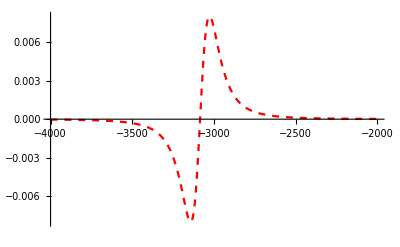

```mathematica
fita100a=Plot[(25019.414243035328 (3085.0469012254393+x))/((10079.224733212714+(3085.0469012254393+x)^2)^2),{x,-4000,-2000}, PlotStyle->{Red, Dashed}, PlotRange->{ {0.047,-0.042}}]
```

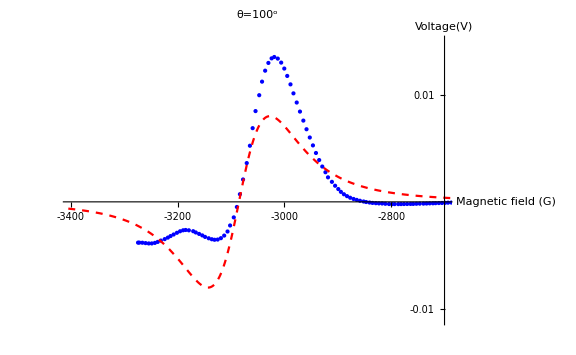

```mathematica
pl100=Show[pa10,  fita100a, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

```mathematica
(*gaussian*)


FindFit[a100 ,-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,{{a,-3100},{v,-250},{s,70}},x]
```

{a→-3092.63,v→-204.928,s→78.2734}

```mathematica
a2hun=NonlinearModelFit[a100, {-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,75<s<80 ,-250<v<-140},{{a,-3100},v,s} ,x ]


a2hun["AdjustedRSquared"]


a2hun["ParameterTable"]

a2hun["BestFit"]
```

FittedModel[0.000171168 ⅇ^(-0.0000820846 (3092.49+x)^2) (3092.49+x)]

0.769336

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-877.935] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3092.49 | 2.49116 | -1241.38 | 0.
v | -203.974 | 12.9768 | -15.7183 | 1.67626×10^-36
s | 78.0466 | 2.58116 | 30.237 | 1.53083×10^-75

0.000171168 ⅇ^(-0.0000820846 (3092.49+x)^2) (3092.49+x)

```mathematica
FindMinimum[0.00017116834843714039 ⅇ^(-0.00008208464479580729 (3092.4930946344543+x)^2) (3092.4930946344543+x),{x,-3150}]


FindMaximum[0.00017116834843714039 ⅇ^(-0.00008208464479580729 (3092.4930946344543+x)^2) (3092.4930946344543+x),{x,-3030}]
```

{-0.00810271,{x→-3170.54}}

{0.00810271,{x→-3014.45}}

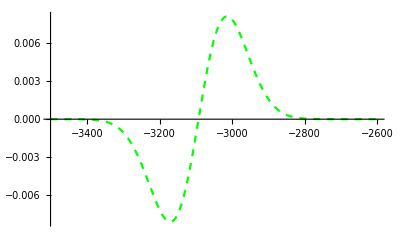

```mathematica
fita100b=Plot[0.00017116834843714039 ⅇ^(-0.00008208464479580729 (3092.4930946344543+x)^2) (3092.4930946344543+x),{x,-3500,-2600}, PlotStyle->{Green, Dashed}, PlotRange->{ {0.047,-0.042}}]
```

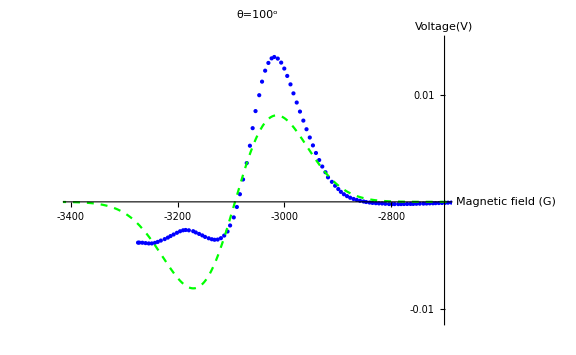

```mathematica
pg100=Show[pa10,  fita100b, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

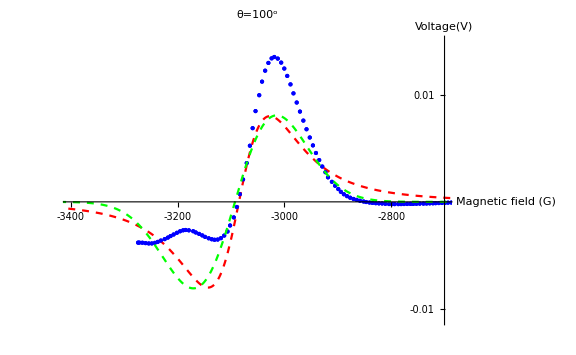

```mathematica
Show[pl100, pg100,ImageSize->Large, AspectRatio->1/GoldenRatio]
```

```mathematica
110 Degrees
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
hten=Import["C:\\Users\\Peggy\\Desktop\\M2.6 ectron Spin Resonance\\EPRdata\\crystal\\110", "Table"];
```

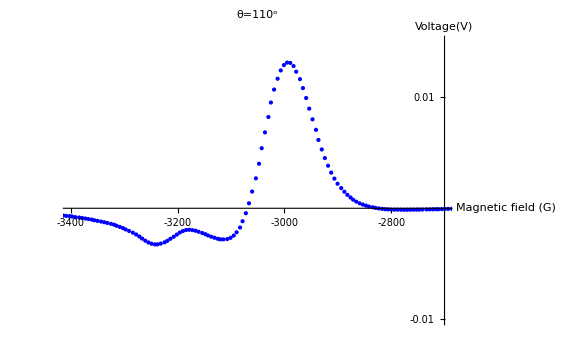

```mathematica
a110=Take[hten, {5,138}];
pa11=ListPlot[a110,PlotRange->{{-3400,-2700}, {0.015,-0.01}} ,LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"θ=110^o" ,   AxesLabel->{"Magnetic field (G)", " Voltage(V)"}, PlotStyle->Directive[Thin,PointSize[Small],Blue], Ticks-> {{-3600,-3400,-3200,-3000,-2800,-2600,-2400},{-0.03,-0.01,0.01,0.03,0.05}}]
```

```mathematica
FindFit[a110, -(v*g (-a+x))/(π (g^2/4+(-a+x)^2)^2),{{a,-3090},g,v},x]
```

{a→-3065.69,g→208.223,v→-383.268}

```mathematica
a1hten=NonlinearModelFit[a110, { -(v*g (-a+x))/(π (g^2/4+(-a+x)^2)^2),190<g<200, -400<v<-300},{{a,-3090},v,g } ,x ]


a1hten["AdjustedRSquared"]

a1hten["ParameterTable"]

a1hten["BestFit"]
```

FittedModel[(22493.8 (3064.18+x))/((9868.81+(«18»+x)^2)^2)]

0.708729

| Estimate | Standard Error | t-Statistic | P-Value
a | -3064.18 | 3.17043 | -966.488 | 2.8777×10^-254
v | -355.672 | 39.5554 | -8.99174 | 2.35897×10^-15
g | 198.684 | 12.7427 | 15.5919 | 1.21431×10^-31

(22493.8 (3064.18+x))/((9868.81+(3064.18+x)^2)^2)

```mathematica
Solve[D[(22493.76953184394 (3064.178297560463+x))/((9868.81080537684+(3064.178297560463+x)^2)^2),x]==0,x]
```

{{x→-3121.53},{x→-3006.82}}

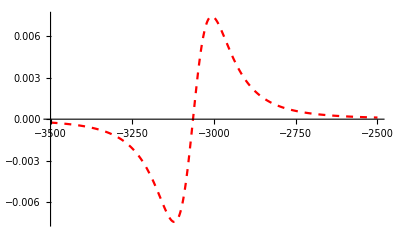

```mathematica
fita110a=Plot[(22493.76953184394 (3064.178297560463+x))/((9868.81080537684+(3064.178297560463+x)^2)^2),{x,-3500,-2500}, PlotStyle->{Red, Dashed}, PlotRange->{ {0.01,-0.01}}]
```

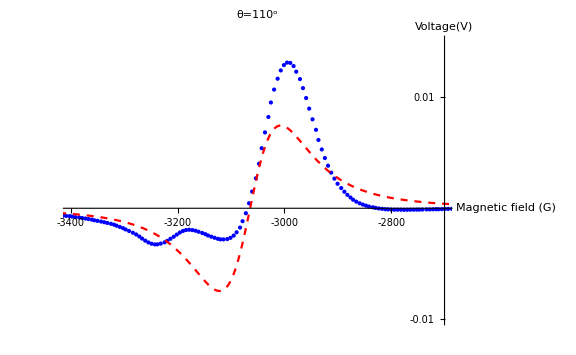

```mathematica
pl110=Show[pa11,  fita110a, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

```mathematica
(*gaussian*)


FindFit[a110 ,-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,{{a,-3070},{v,-300},{s,70}},x]
```

{a→-3076.17,v→-206.374,s→83.2268}

```mathematica
a2hten=NonlinearModelFit[a110, {-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,80<s<85 ,-250<v<-140},{{a,-3080},v,s} ,x ]


a2hten["AdjustedRSquared"]


a2hten["ParameterTable"]

a2hten["BestFit"]
```

FittedModel[0.000145859 ⅇ^(-0.0000743496 (3075.31+x)^2) (3075.31+x)]

0.715832

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3075.31 | 3.63152 | -846.837 | 9.47959×10^-247
v | -201.632 | 17.2922 | -11.6603 | 5.42786×10^-22
s | 82.006 | 3.63194 | 22.5791 | 5.38885×10^-47

0.000145859 ⅇ^(-0.0000743496 (3075.31+x)^2) (3075.31+x)

```mathematica
FindMinimum[0.0001458588488251062 ⅇ^(-0.00007434958255725404 (3075.3108199822595+x)^2) (3075.3108199822595+x),{x,-3120}]


FindMaximum[0.0001458588488251062 ⅇ^(-0.00007434958255725404 (3075.3108199822595+x)^2) (3075.3108199822595+x),{x,-3000}]
```

{-0.0072549,{x→-3157.32}}

{0.0072549,{x→-2993.3}}

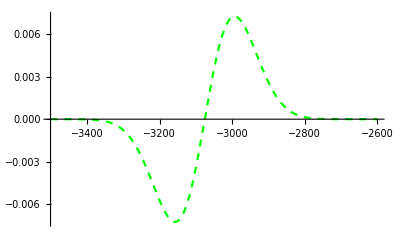

```mathematica
fita110b=Plot[0.0001458588488251062 ⅇ^(-0.00007434958255725404 (3075.3108199822595+x)^2) (3075.3108199822595+x),{x,-3500,-2600}, PlotStyle->{Green, Dashed}, PlotRange->{ {0.047,-0.042}}]
```

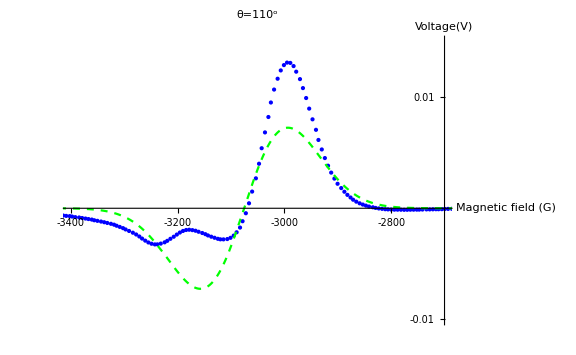

```mathematica
pg110=Show[pa11,  fita110b, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

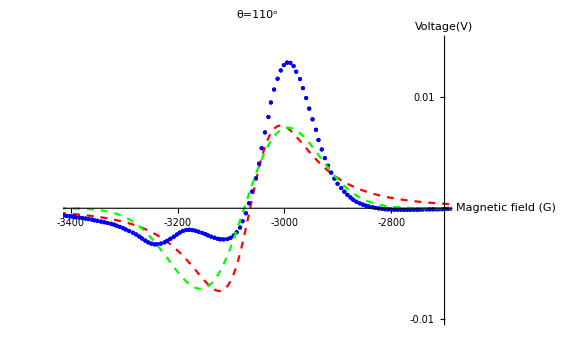

```mathematica
Show[pl110, pg110,ImageSize->Large, AspectRatio->1/GoldenRatio]
```

```mathematica
120 Degrees
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
htwn=Import["C:\\Users\\Peggy\\Desktop\\M2.6 ectron Spin Resonance\\EPRdata\\crystal\\120", "Table"];
```

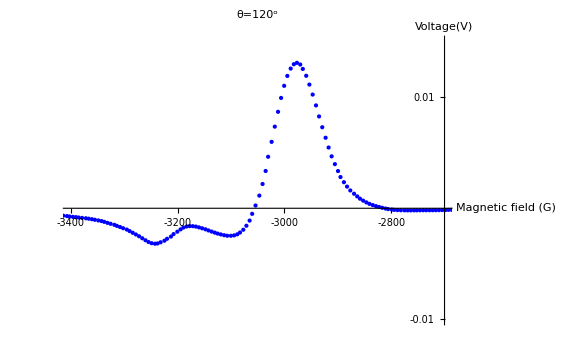

```mathematica
a120=Take[htwn, {5,184}];
pa12=ListPlot[a120,PlotRange->{{-3400,-2700}, {0.015,-0.01}} ,LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"θ=120^o" ,   AxesLabel->{"Magnetic field (G)", " Voltage(V)"}, PlotStyle->Directive[Thin,PointSize[Small],Blue], Ticks-> {{-3600,-3400,-3200,-3000,-2800,-2600,-2400},{-0.03,-0.01,0.01,0.03,0.05}}]
```

```mathematica
FindFit[a120,  -(v*g (-a+x))/(π (g^2/4+(-a+x)^2)^2),{{a,-3070},g,v},x]
```

{a→-3051.33,g→-210.505,v→375.246}

```mathematica
a1htwn=NonlinearModelFit[a120, { -(v*g (-a+x))/(π (g^2/4+(-a+x)^2)^2),200<g<220, -400<v<-300},{{a,-3052},v,g } ,x ]


a1htwn["AdjustedRSquared"]

a1htwn["ParameterTable"]

a1htwn["BestFit"]
```

FittedModel[(24423.5 (3050.97+x))/((10857.3+(«18»+x)^2)^2)]

0.682756

| Estimate | Standard Error | t-Statistic | P-Value
a | -3050.97 | 3.05623 | -998.278 | 0.
v | -368.185 | 37.4544 | -9.83022 | 1.79975×10^-18
g | 208.397 | 12.2327 | 17.036 | 3.73018×10^-39

(24423.5 (3050.97+x))/((10857.3+(3050.97+x)^2)^2)

```mathematica
88888
```

```mathematica
Solve[D[(24423.49709954495 (3050.971471495517+x))/((10857.319796846657+(3050.971471495517+x)^2)^2),x]==0,x]
```

{{x→-3111.13},{x→-2990.81}}

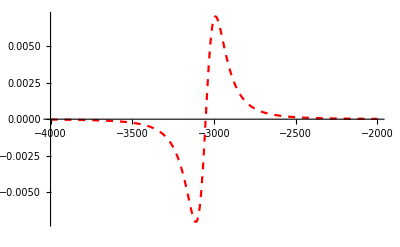

```mathematica
fita120a=Plot[(24423.49709954495 (3050.971471495517+x))/((10857.319796846657+(3050.971471495517+x)^2)^2),{x,-4000,-2000}, PlotStyle->{Red, Dashed}, PlotRange->{ {0.047,-0.042}}]
```

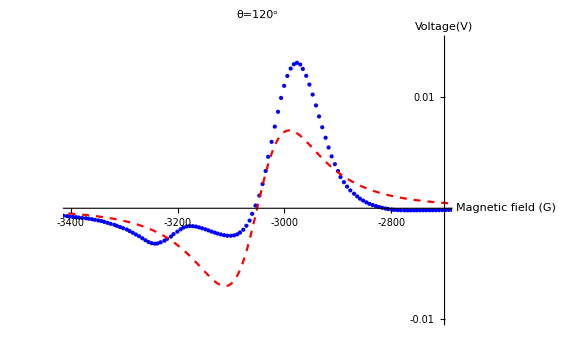

```mathematica
pl120=Show[pa12,  fita120a, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

```mathematica
(*gaussian*)


FindFit[a120 ,-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,{{a,-3100},{v,-270},{s,80}},x]
```

{a→-3063.64,v→-207.776,s→85.7717}

```mathematica
a2htwn=NonlinearModelFit[a120, {-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,80<s<90 ,-250<v<-140},{{a,-3065},v,s} ,x ]


a2htwn["AdjustedRSquared"]


a2htwn["ParameterTable"]

a2htwn["BestFit"]
```

FittedModel[0.000131923 ⅇ^(-0.0000684021 (3063.43+x)^2) (3063.43+x)]

0.686567

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-743.529] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3063.43 | 3.5061 | -873.741 | 1.×10^-323
v | -206.662 | 16.4121 | -12.592 | 2.25158×10^-26
s | 85.4969 | 3.50639 | 24.3831 | 1.76922×10^-58

0.000131923 ⅇ^(-0.0000684021 (3063.43+x)^2) (3063.43+x)

```mathematica
FindMinimum[0.00013192294855543277 ⅇ^(-0.00006840214528655748 (3063.427425806121+x)^2) (3063.427425806121+x),{x,-3100}]


FindMaximum[0.00013192294855543277 ⅇ^(-0.00006840214528655748 (3063.427425806121+x)^2) (3063.427425806121+x),{x,-3000}]
```

{-0.00684106,{x→-3148.92}}

{0.00684106,{x→-2977.93}}

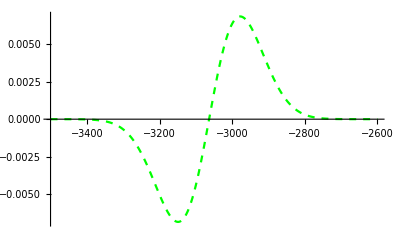

```mathematica
fita120b=Plot[0.00013192294855543277 ⅇ^(-0.00006840214528655748 (3063.427425806121+x)^2) (3063.427425806121+x),{x,-3500,-2600}, PlotStyle->{Green, Dashed}, PlotRange->{ {0.047,-0.042}}]
```

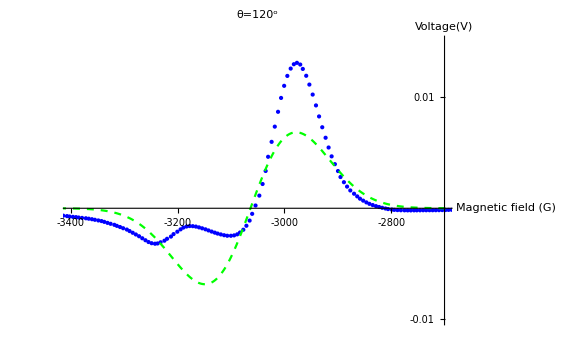

```mathematica
pg120=Show[pa12,  fita120b, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

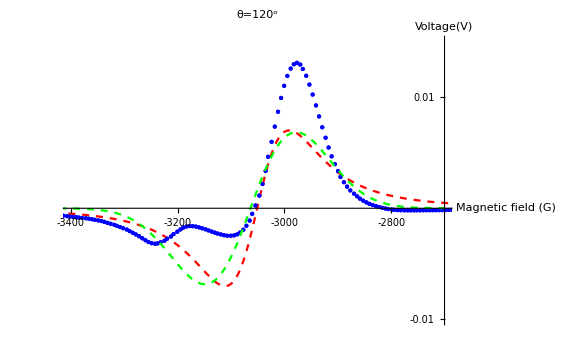

```mathematica
Show[pl120, pg120,ImageSize->Large, AspectRatio->1/GoldenRatio]
```

```mathematica
130 Degrees
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
htht=Import["C:\\Users\\Peggy\\Desktop\\M2.6 ectron Spin Resonance\\EPRdata\\crystal\\130", "Table"];
```

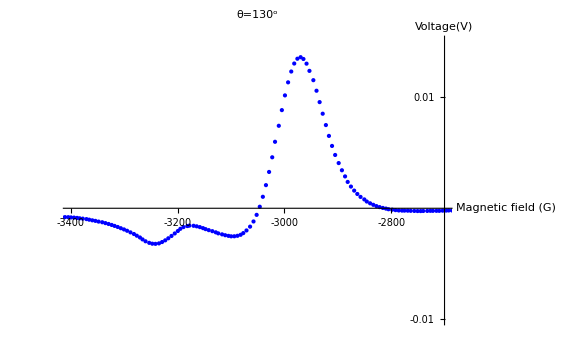

```mathematica
a130=Take[htht, {5,145}];
pa13=ListPlot[a130,PlotRange->{{-3400,-2700}, {0.015,-0.01}} ,LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"θ=130^o" ,   AxesLabel->{"Magnetic field (G)", " Voltage(V)"}, PlotStyle->Directive[Thin,PointSize[Small],Blue], Ticks-> {{-3600,-3400,-3200,-3000,-2800,-2600,-2400},{-0.03,-0.01,0.01,0.03,0.05}}]
```

```mathematica
FindFit[a130,  -(v*g (-a+x))/(π (g^2/4+(-a+x)^2)^2),{{a,-3050},g,v},x]
```

{a→-3043.11,g→-207.483,v→375.847}

```mathematica
a1htht=NonlinearModelFit[a130, { -(v*g (-a+x))/(π (g^2/4+(-a+x)^2)^2),200<g<210, -400<v<-300},{{a,-3050},v,g } ,x ]


a1htht["AdjustedRSquared"]

a1htht["ParameterTable"]

a1htht["BestFit"]
```

FittedModel[(23543.6 (3042.39+x))/((10339.5+(«19»+x)^2)^2)]

0.673345

| Estimate | Standard Error | t-Statistic | P-Value
a | -3042.39 | 3.44441 | -883.283 | 8.23762×10^-261
v | -363.7 | 42.8913 | -8.47957 | 3.09348×10^-14
g | 203.367 | 13.8275 | 14.7074 | 4.79642×10^-30

(23543.6 (3042.39+x))/((10339.5+(3042.39+x)^2)^2)

```mathematica
Solve[D[(23543.608455130452 (3042.3867956967674+x))/((10339.489517952356+(3042.3867956967674+x)^2)^2),x]==0,x]
```

{{x→-3101.09},{x→-2983.68}}

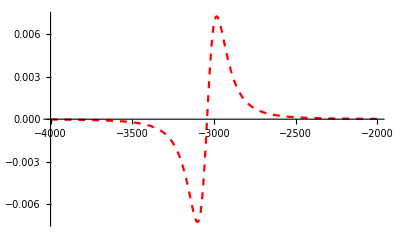

```mathematica
fita130a=Plot[(23543.608455130452 (3042.3867956967674+x))/((10339.489517952356+(3042.3867956967674+x)^2)^2),{x,-4000,-2000}, PlotStyle->{Red, Dashed}, PlotRange->{ {0.047,-0.042}}]
```

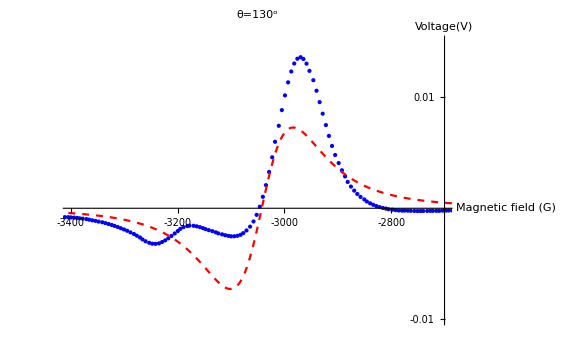

```mathematica
pl130=Show[pa13,  fita130a, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

```mathematica
(*gaussian*)


FindFit[a130 ,-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,{{a,-3070},{v,-250},{s,75}},x]
```

{a→-3054.04,v→-202.52,s→83.0804}

```mathematica
a2htht=NonlinearModelFit[a130, {-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,80<s<85 ,-200<v<-140},{{a,-3070},v,s} ,x ]


a2htht["AdjustedRSquared"]


a2htht["ParameterTable"]

a2htht["BestFit"]
```

FittedModel[0.000145375 ⅇ^(-0.000076276 (3052.4+x)^2) (3052.4+x)]

0.674762

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3052.4 | 3.87814 | -787.078 | 6.6951×10^-254
v | -193.399 | 17.9266 | -10.7884 | 4.67388×10^-20
s | 80.9638 | 3.87041 | 20.9186 | 1.24057×10^-44

0.000145375 ⅇ^(-0.000076276 (3052.4+x)^2) (3052.4+x)

```mathematica
FindMinimum[0.000145375258028739 ⅇ^(-0.00007627602188324928 (3052.396804319983+x)^2) (3052.396804319983+x),{x,-3100}]


FindMaximum[0.000145375258028739 ⅇ^(-0.00007627602188324928 (3052.396804319983+x)^2) (3052.396804319983+x),{x,-2980}]
```

{-0.00713895,{x→-3133.36}}

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.00713895,{x→-2971.43}}

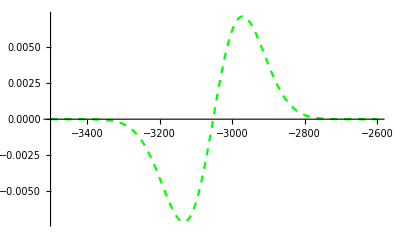

```mathematica
fita130b=Plot[0.000145375258028739 ⅇ^(-0.00007627602188324928 (3052.396804319983+x)^2) (3052.396804319983+x),{x,-3500,-2600}, PlotStyle->{Green, Dashed}, PlotRange->{ {0.047,-0.042}}]
```

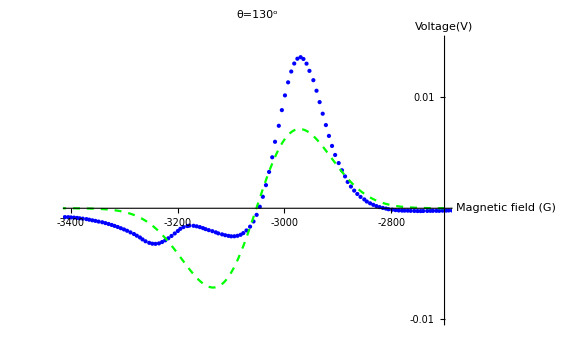

```mathematica
pg130=Show[pa13,  fita130b, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

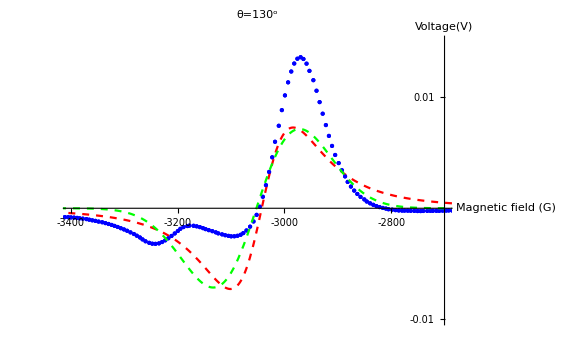

```mathematica
Show[pl130, pg130,ImageSize->Large, AspectRatio->1/GoldenRatio]
```

```mathematica
140 Degrees
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
hft=Import["C:\\Users\\Peggy\\Desktop\\M2.6 ectron Spin Resonance\\EPRdata\\crystal\\140", "Table"];
```

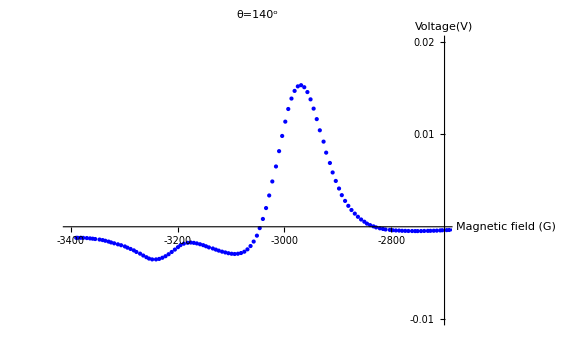

```mathematica
a140=Take[hft, {5,139}];
pa14=ListPlot[a140,PlotRange->{{-3400,-2700}, {0.02,-0.01}} ,LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"θ=140^o" ,   AxesLabel->{"Magnetic field (G)", " Voltage(V)"}, PlotStyle->Directive[Thin,PointSize[Small],Blue], Ticks-> {{-3600,-3400,-3200,-3000,-2800,-2600,-2400},{-0.03,-0.01,0.01,0.02,0.05}}]
```

```mathematica
FindFit[a140, -(v*g (-a+x))/(π (g^2/4+(-a+x)^2)^2),{{a,-3050},g,v},x]
```

{a→-3040.31,g→-197.17,v→385.536}

```mathematica
a1hft=NonlinearModelFit[a140, { -(v*g (-a+x))/(π (g^2/4+(-a+x)^2)^2),190<g<200, -400<v<-300},{{a,-3050},v,g } ,x ]


a1hft["AdjustedRSquared"]

a1hft["ParameterTable"]

a1hft["BestFit"]
```

FittedModel[(23714.9 (3040.09+x))/((9591.42+(«19»+x)^2)^2)]

0.668762

| Estimate | Standard Error | t-Statistic | P-Value
a | -3040.09 | 3.41012 | -891.489 | 2.39139×10^-251
v | -380.364 | 46.2333 | -8.22706 | 1.60249×10^-13
g | 195.872 | 13.7419 | 14.2536 | 1.73077×10^-28

(23714.9 (3040.09+x))/((9591.42+(3040.09+x)^2)^2)

```mathematica
Solve[D[(23714.90658143773 (3040.0892681695136+x))/((9591.419837489138+(3040.0892681695136+x)^2)^2),x]==0,x]
```

{{x→-3096.63},{x→-2983.55}}

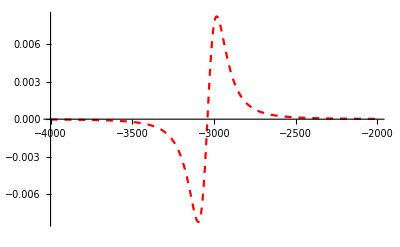

```mathematica
fita140a=Plot[(23714.90658143773 (3040.0892681695136+x))/((9591.419837489138+(3040.0892681695136+x)^2)^2),{x,-4000,-2000}, PlotStyle->{Red, Dashed}, PlotRange->{ {0.047,-0.042}}]
```

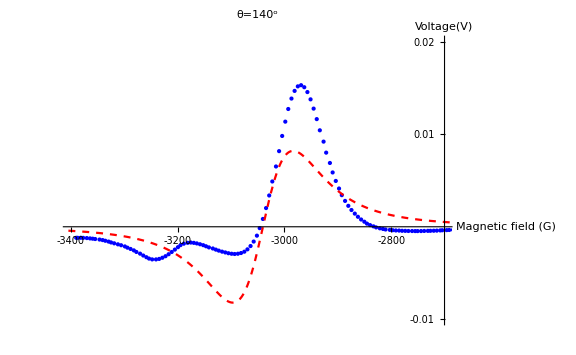

```mathematica
pl140=Show[pa14,  fita140a, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

```mathematica
(*gaussian*)


FindFit[a140 ,-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,{{a,-3060},{v,-200},{s,70}},x]
```

{a→-3047.34,v→-195.332,s→75.7829}

```mathematica
a2hft=NonlinearModelFit[a140, {-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,70<s<80 ,-200<v<-150},{{a,-3050},v,s} ,x ]


a2hft["AdjustedRSquared"]


a2hft["ParameterTable"]

a2hft["BestFit"]
```

FittedModel[0.000184202 ⅇ^(-0.0000912304 (3046.01+x)^2) (3046.01+x)]

0.67088

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3046.01 | 3.64186 | -836.389 | 1.08508×10^-247
v | -187.339 | 17.845 | -10.4982 | 4.06498×10^-19
s | 74.0313 | 3.64335 | 20.3196 | 1.82713×10^-42

0.000184202 ⅇ^(-0.0000912304 (3046.01+x)^2) (3046.01+x)

```mathematica
FindMinimum[0.00018420179257258105 ⅇ^(-0.00009123042947825654 (3046.0089510501207+x)^2) (3046.0089510501207+x),{x,-3100}]


FindMaximum[0.00018420179257258105 ⅇ^(-0.00009123042947825654 (3046.0089510501207+x)^2) (3046.0089510501207+x),{x,-3000}]
```

{-0.00827107,{x→-3120.04}}

{0.00827107,{x→-2971.98}}

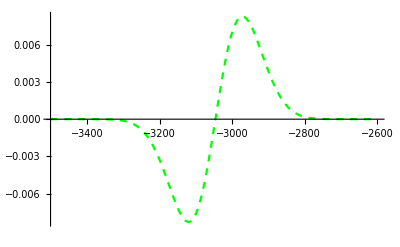

```mathematica
fita140b=Plot[0.00018420179257258105 ⅇ^(-0.00009123042947825654 (3046.0089510501207+x)^2) (3046.0089510501207+x),{x,-3500,-2600}, PlotStyle->{Green, Dashed}, PlotRange->{ {0.047,-0.042}}]
```

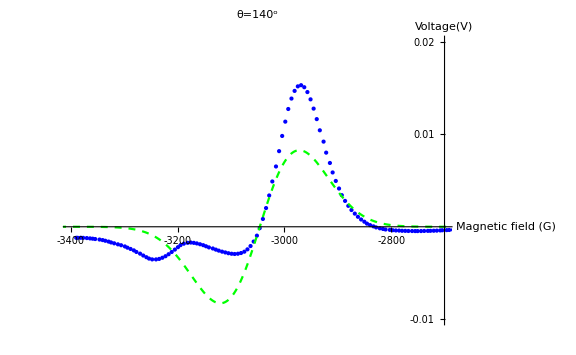

```mathematica
pg140=Show[pa14,  fita140b, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

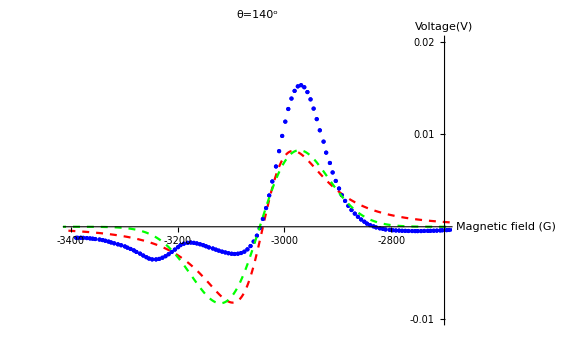

```mathematica
Show[pl140, pg140,ImageSize->Large, AspectRatio->1/GoldenRatio]
```

```mathematica
150 Degrees
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
hfft=Import["C:\\Users\\Peggy\\Desktop\\M2.6 ectron Spin Resonance\\EPRdata\\crystal\\150", "Table"];
```

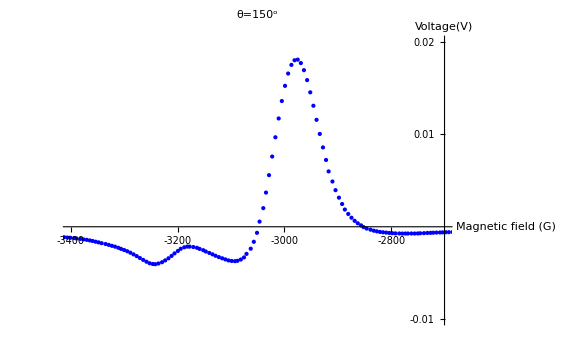

```mathematica
a150=Take[hfft, {5,201}];
pa15=ListPlot[a150,PlotRange->{{-3400,-2700}, {0.02,-0.01}} ,LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"θ=150^o" ,   AxesLabel->{"Magnetic field (G)", " Voltage(V)"}, PlotStyle->Directive[Thin,PointSize[Small],Blue], Ticks-> {{-3600,-3400,-3200,-3000,-2800,-2600,-2400},{-0.03,-0.01,0.01,0.02,0.05}}]
```

```mathematica
FindFit[a150,  -(v*g (-a+x))/(π (g^2/4+(-a+x)^2)^2),{{a,-3040},g,v},x]
```

{a→-3044.3,g→-184.781,v→407.857}

```mathematica
a1hfft=NonlinearModelFit[a150, { -(v*g (-a+x))/(π (g^2/4+(-a+x)^2)^2),180<g<190, -500<v<-400},{{a,-3040},v,g } ,x ]


a1hfft["AdjustedRSquared"]

a1hfft["ParameterTable"]

a1hfft["BestFit"]
```

FittedModel[(24043.3 (3044.3+x))/((8538.07+(«18»+x)^2)^2)]

0.673803

| Estimate | Standard Error | t-Statistic | P-Value
a | -3044.3 | 2.62087 | -1161.56 | 0.
v | -408.728 | 40.3532 | -10.1288 | 1.26256×10^-19
g | 184.803 | 10.535 | 17.5419 | 6.83183×10^-42

(24043.3 (3044.3+x))/((8538.07+(3044.3+x)^2)^2)

```mathematica
Solve[D[(24043.329492888108 (3044.303515065919+x))/((8538.07351775629+(3044.303515065919+x)^2)^2),x]==0,x]
```

{{x→-3097.65},{x→-2990.96}}

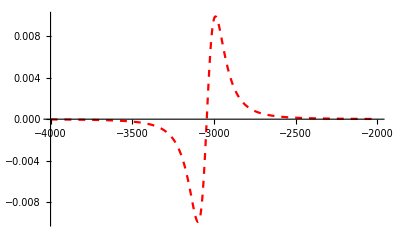

```mathematica
fita150a=Plot[(24043.329492888108 (3044.303515065919+x))/((8538.07351775629+(3044.303515065919+x)^2)^2),{x,-4000,-2000}, PlotStyle->{Red, Dashed}, PlotRange->{ {0.047,-0.042}}]
```

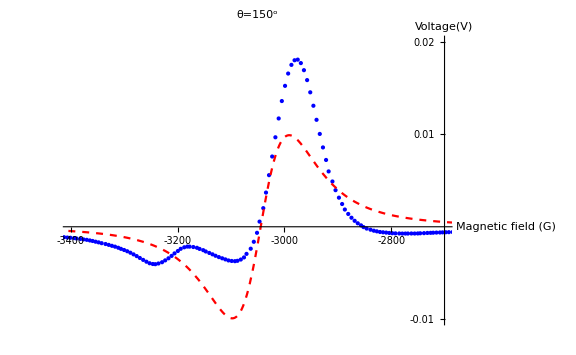

```mathematica
pl150=Show[pa15,  fita150a, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

```mathematica
(*gaussian*)


FindFit[a150 ,-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,{{a,-3050},{v,-200},{s,60}},x]
```

{a→-3049.14,v→-198.496,s→69.1011}

```mathematica
a2hfft=NonlinearModelFit[a150, {-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,70<s<75 ,-200<v<-170},{{a,-3050},v,s} ,x ]


a2hfft["AdjustedRSquared"]


a2hfft["ParameterTable"]

a2hfft["BestFit"]
```

FittedModel[0.000228247 ⅇ^(-0.000101604 (3049.9+x)^2) (3049.9+x)]

0.675286

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-842.41] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3049.9 | 2.89055 | -1055.13 | 0.
v | -197.507 | 15.7833 | -12.5136 | 1.00204×10^-26
s | 70.1502 | 2.89333 | 24.2455 | 1.26736×10^-60

0.000228247 ⅇ^(-0.000101604 (3049.9+x)^2) (3049.9+x)

```mathematica
FindMinimum[0.00022824677563162168 ⅇ^(-0.00010160429472935159 (3049.8968073135698+x)^2) (3049.8968073135698+x),{x,-3100}]


FindMaximum[0.00022824677563162168 ⅇ^(-0.00010160429472935159 (3049.8968073135698+x)^2) (3049.8968073135698+x),{x,-3000}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{-0.0097115,{x→-3120.05}}

{0.0097115,{x→-2979.75}}

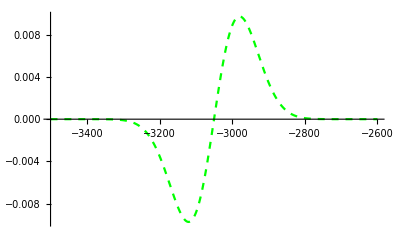

```mathematica
fita150b=Plot[0.00022824677563162168 ⅇ^(-0.00010160429472935159 (3049.8968073135698+x)^2) (3049.8968073135698+x),{x,-3500,-2600}, PlotStyle->{Green, Dashed}, PlotRange->{ {0.047,-0.042}}]
```

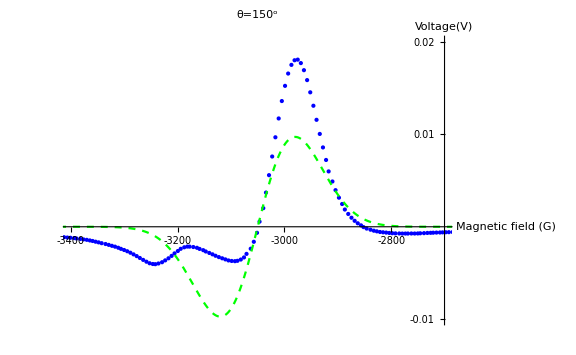

```mathematica
pg150=Show[pa15,  fita150b, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

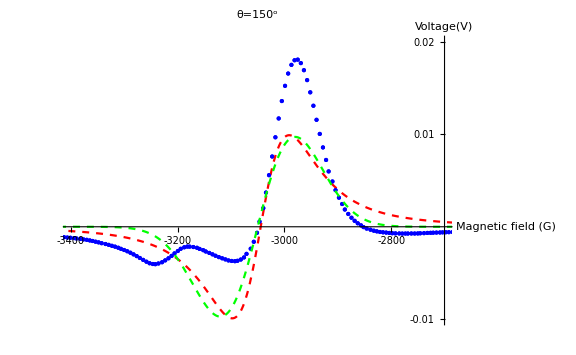

```mathematica
Show[pl150, pg150,ImageSize->Large, AspectRatio->1/GoldenRatio]
```

```mathematica
160 Degrees
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
hsxt=Import["C:\\Users\\Peggy\\Desktop\\M2.6 ectron Spin Resonance\\EPRdata\\crystal\\160", "Table"];
```

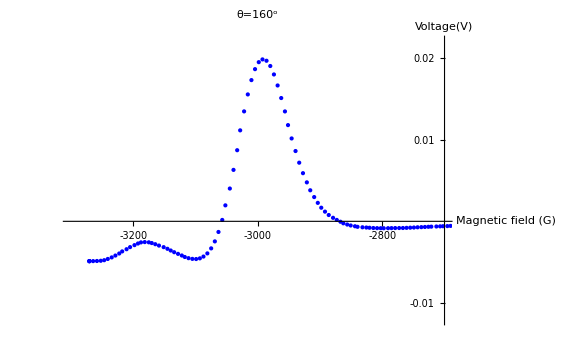

```mathematica
a160=Take[hsxt, {5,126}];
pa16=ListPlot[a160,PlotRange->{{-3300,-2700}, {0.022,-0.012}} ,LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"θ=160^o" ,   AxesLabel->{"Magnetic field (G)", " Voltage(V)"}, PlotStyle->Directive[Thin,PointSize[Small],Blue], Ticks-> {{-3600,-3400,-3200,-3000,-2800,-2600,-2400},{-0.03,-0.01,0.01,0.02,0.05}}]
```

```mathematica
FindFit[a160,  -(v*g (-a+x))/(π (g^2/4+(-a+x)^2)^2),{{a,-3060},g,v},x]
```

{a→-3053.39,g→-171.891,v→403.971}

```mathematica
a1hsxt=NonlinearModelFit[a160, { -(v*g (-a+x))/(π (g^2/4+(-a+x)^2)^2),170<g<180, -450<v<-350},{{a,-3050},v,g } ,x ]


a1hsxt["AdjustedRSquared"]

a1hsxt["ParameterTable"]

a1hsxt["BestFit"]
```

FittedModel[(22052.7 (3053.37+x))/((7375.74+(«18»+x)^2)^2)]

0.69091

| Estimate | Standard Error | t-Statistic | P-Value
a | -3053.37 | 2.98544 | -1022.75 | 1.558×10^-236
v | -403.346 | 49.2195 | -8.19484 | 3.28052×10^-13
g | 171.764 | 12.0887 | 14.2087 | 2.13279×10^-27

(22052.7 (3053.37+x))/((7375.74+(3053.37+x)^2)^2)

```mathematica
Solve[D[(22052.660020443593 (3053.370648639863+x))/((7375.74281405845+(3053.370648639863+x)^2)^2),x]==0,x]
```

{{x→-3102.95},{x→-3003.79}}

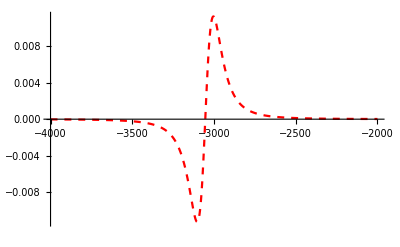

```mathematica
fita160a=Plot[(22052.660020443593 (3053.370648639863+x))/((7375.74281405845+(3053.370648639863+x)^2)^2),{x,-4000,-2000}, PlotStyle->{Red, Dashed}, PlotRange->{ {0.047,-0.042}}]
```

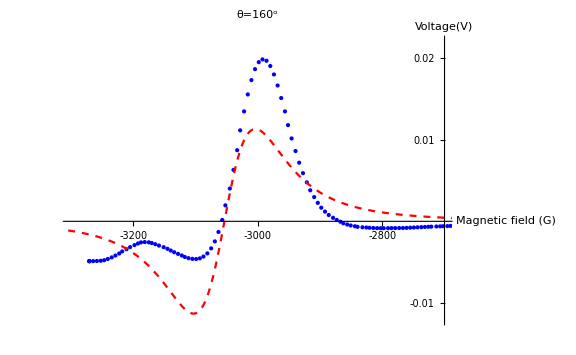

```mathematica
pl160=Show[pa16,  fita160a, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

```mathematica
(*gaussian*)


FindFit[a160 ,-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,{{a,-3060},{v,-250},{s,60}},x]
```

{a→-3058.44,v→-203.645,s→65.8232}

```mathematica
a2hsxt=NonlinearModelFit[a160, {-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,60<s<70 ,-250<v<-200},{{a,-3060},v,s} ,x ]


a2hsxt["AdjustedRSquared"]


a2hsxt["ParameterTable"]

a2hsxt["BestFit"]
```

FittedModel[0.000285057 ⅇ^(-0.000115302 (3058.46+x)^2) (3058.46+x)]

0.696902

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3058.46 | 3.19389 | -957.598 | 3.92813×10^-233
v | -204.042 | 19.1167 | -10.6735 | 4.57822×10^-19
s | 65.8516 | 3.18737 | 20.6601 | 3.59132×10^-41

0.000285057 ⅇ^(-0.000115302 (3058.46+x)^2) (3058.46+x)

```mathematica
FindMinimum[0.0002850570831628286 ⅇ^(-0.00011530226530026067 (3058.462289814986+x)^2) (3058.462289814986+x),{x,-3100}]


FindMaximum[0.0002850570831628286 ⅇ^(-0.00011530226530026067 (3058.462289814986+x)^2) (3058.462289814986+x),{x,-3000}]
```

{-0.0113855,{x→-3124.31}}

{0.0113855,{x→-2992.61}}

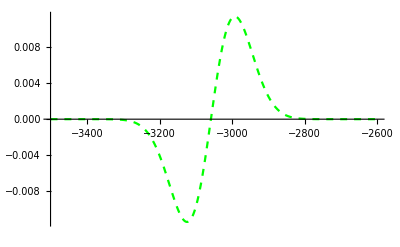

```mathematica
fita160b=Plot[0.0002850570831628286 ⅇ^(-0.00011530226530026067 (3058.462289814986+x)^2) (3058.462289814986+x),{x,-3500,-2600}, PlotStyle->{Green, Dashed}, PlotRange->{ {0.047,-0.042}}]
```

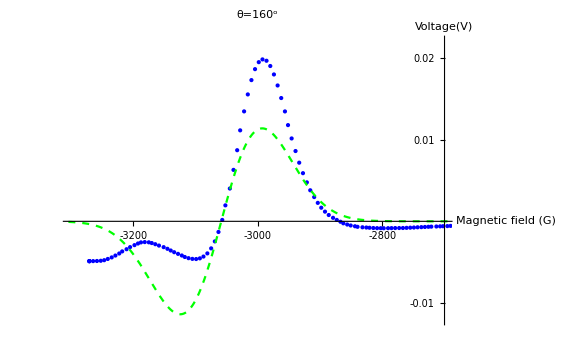

```mathematica
pg160=Show[pa16,  fita160b, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

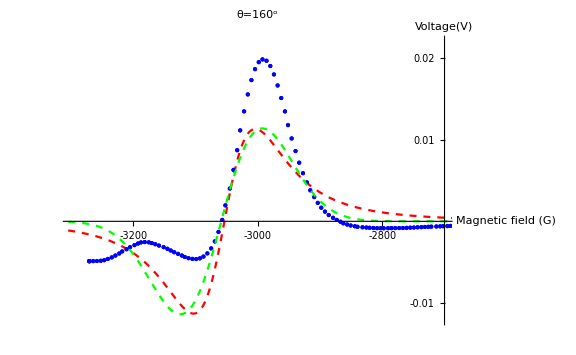

```mathematica
Show[pl160, pg160,ImageSize->Large, AspectRatio->1/GoldenRatio]
```

```mathematica
170 Degrees
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
hsvt=Import["C:\\Users\\Peggy\\Desktop\\M2.6 ectron Spin Resonance\\EPRdata\\crystal\\170", "Table"];
```

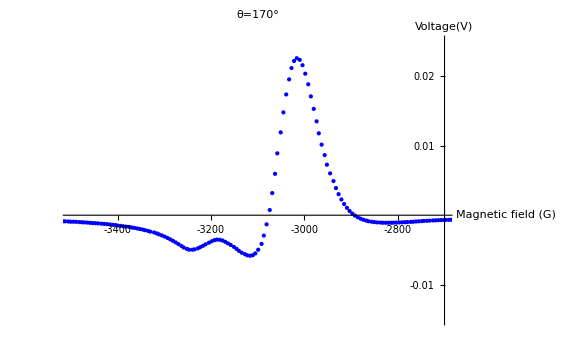

```mathematica
a170=Take[hsvt, {5,203}];
pa17=ListPlot[a170,PlotRange->{{-3500,-2700}, {0.025,-0.015}} ,LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"θ=170°" ,   AxesLabel->{"Magnetic field (G)", " Voltage(V)"}, PlotStyle->Directive[Thin,PointSize[Small],Blue], Ticks-> {{-3600,-3400,-3200,-3000,-2800,-2600,-2400},{-0.03,-0.01,0.01,0.02,0.05}}]
```

```mathematica
FindFit[a170,  -(v*g (-a+x))/(π (g^2/4+(-a+x)^2)^2),{{a,-3080},g,v},x]
```

{a→-3073.73,g→-167.879,v→453.675}

```mathematica
a1hsvt=NonlinearModelFit[a170, { -(v*g (-a+x))/(π (g^2/4+(-a+x)^2)^2),160<g<170, -500<v<-400},{{a,-3075},v,g } ,x ]


a1hsvt["AdjustedRSquared"]

a1hsvt["ParameterTable"]

a1hsvt["BestFit"]
```

FittedModel[(23782. (3073.54+x))/((6941.26+(«19»+x)^2)^2)]

0.724375

| Estimate | Standard Error | t-Statistic | P-Value
a | -3073.54 | 2.10352 | -1461.14 | 0.
v | -448.383 | 39.2762 | -11.4162 | 1.79555×10^-23
g | 166.628 | 8.43025 | 19.7655 | 1.51519×10^-48

(23782. (3073.54+x))/((6941.26+(3073.54+x)^2)^2)

```mathematica
Solve[D[(23782.007490564865 (3073.5431500806258+x))/((6941.2622669016355+(3073.5431500806258+x)^2)^2),x]==0,x]
```

{{x→-3121.64},{x→-3025.44}}

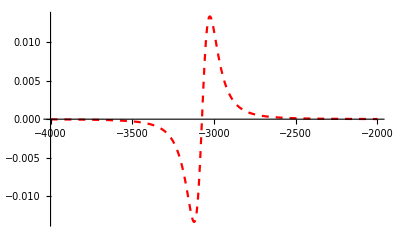

```mathematica
fita170a=Plot[(23782.007490564865 (3073.5431500806258+x))/((6941.2622669016355+(3073.5431500806258+x)^2)^2),{x,-4000,-2000}, PlotStyle->{Red, Dashed}, PlotRange->{ {0.047,-0.042}}]
```

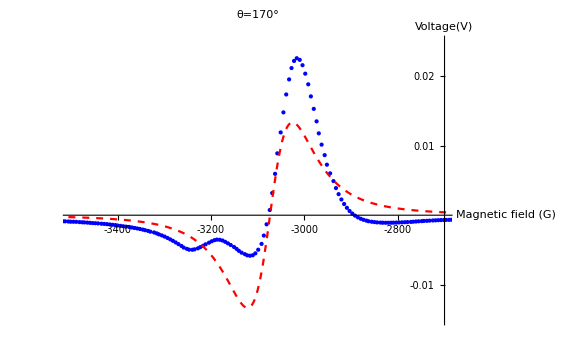

```mathematica
pl170=Show[pa17,  fita170a, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

```mathematica
(*gaussian*)


FindFit[a170 ,-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,{{a,-3080},{v,-250},{s,50}},x]
```

{a→-3078.68,v→-228.833,s→64.4568}

```mathematica
a2hsvt=NonlinearModelFit[a170, {-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,50<s<60 ,-230<v<-204},{{a,-3080},v,s} ,x ]


a2hsvt["AdjustedRSquared"]


a2hsvt["ParameterTable"]

a2hsvt["BestFit"]
```

FittedModel[0.000381535 ⅇ^(-0.000139409 (3075.74+x)^2) (3075.74+x)]

0.719019

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-908.952] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3075.74 | 2.15847 | -1424.96 | 0.
v | -205.42 | 14.3267 | -14.3383 | 2.34098×10^-32
s | 59.8879 | 2.15477 | 27.7932 | 6.43707×10^-70

0.000381535 ⅇ^(-0.000139409 (3075.74+x)^2) (3075.74+x)

```mathematica
FindMinimum[0.00038153546567183596 ⅇ^(-0.00013940914257753103 (3075.735060427774+x)^2) (3075.735060427774+x),{x,-3100}]


FindMaximum[0.00038153546567183596 ⅇ^(-0.00013940914257753103 (3075.735060427774+x)^2) (3075.735060427774+x),{x,-3000}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{-0.0138588,{x→-3135.62}}

{0.0138588,{x→-3015.85}}

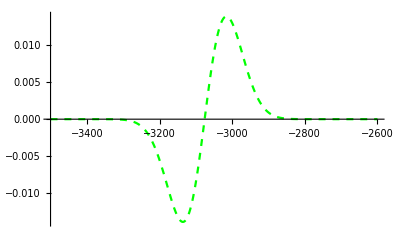

```mathematica
fita170b=Plot[0.00038153546567183596 ⅇ^(-0.00013940914257753103 (3075.735060427774+x)^2) (3075.735060427774+x),{x,-3500,-2600}, PlotStyle->{Green, Dashed}, PlotRange->{ {0.047,-0.042}}]
```

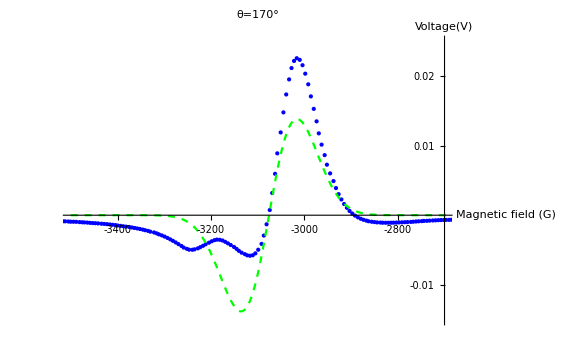

```mathematica
pg170=Show[pa17,  fita170b, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

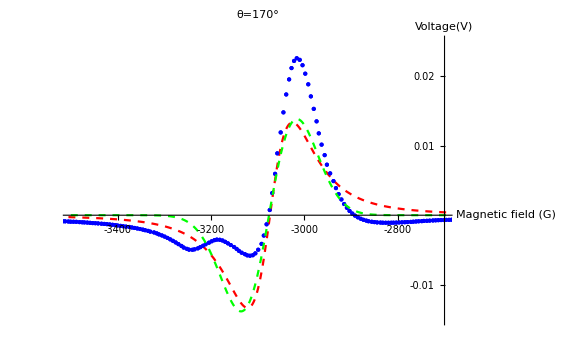

```mathematica
Show[pl170, pg170,ImageSize->Large, AspectRatio->1/GoldenRatio]
```

```mathematica
190 Degrees
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
hnin=Import["C:\\Users\\Peggy\\Desktop\\M2.6 ectron Spin Resonance\\EPRdata\\crystal\\190", "Table"];
```

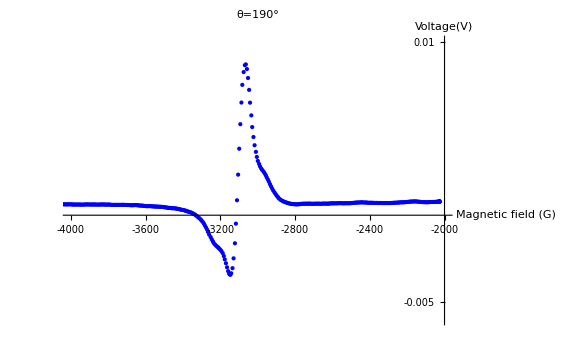

```mathematica
a190=Take[hnin, {5,362}];
pa19=ListPlot[a190,PlotRange->{{-4000,-2000}, {0.01,-0.006}} ,LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"θ=190°" ,   AxesLabel->{"Magnetic field (G)", " Voltage(V)"}, PlotStyle->Directive[Thin,PointSize[Small],Blue], Ticks-> {{-4000,-3800,-3600,-3400,-3200,-3000,-2800,-2600,-2400,-2200,-2000},{-0.01,-0.005,0.01}}]
```

```mathematica
FindFit[a190, -(v*g (-a+x))/(π (g^2/4+(-a+x)^2)^2),{{a,-3120},g,v},x]
```

{a→-3110.82,g→-146.211,v→151.198}

```mathematica
a1hnin=NonlinearModelFit[a190, { -(v*g (-a+x))/(π (g^2/4+(-a+x)^2)^2),140<g<150, -200<v<-100},{{a,-3110},v,g } ,x ]


a1hnin["AdjustedRSquared"]

a1hnin["ParameterTable"]

a1hnin["BestFit"]
```

FittedModel[(6866.2 (3110.72+x))/((5245.09+(«19»+x)^2)^2)]

0.748435

| Estimate | Standard Error | t-Statistic | P-Value
a | -3110.72 | 1.28404 | -2422.6 | 0.
v | -148.922 | 9.14156 | -16.2907 | 5.98674×10^-45
g | 144.846 | 5.14653 | 28.1444 | 1.96031×10^-92

(6866.2 (3110.72+x))/((5245.09+(3110.72+x)^2)^2)

```mathematica
Solve[D[(6866.200828601439 (3110.7202947199594+x))/((5245.085000627543+(3110.7202947199594+x)^2)^2),x]==0,x]
```

{{x→-3152.53},{x→-3068.91}}

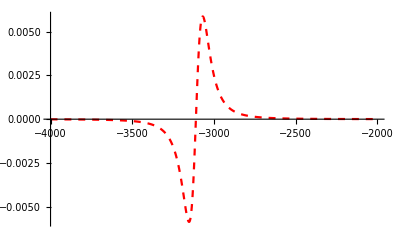

```mathematica
fita190a=Plot[(6866.200828601439 (3110.7202947199594+x))/((5245.085000627543+(3110.7202947199594+x)^2)^2),{x,-4000,-2000}, PlotStyle->{Red, Dashed}, PlotRange->{ {0.047,-0.042}}]
```

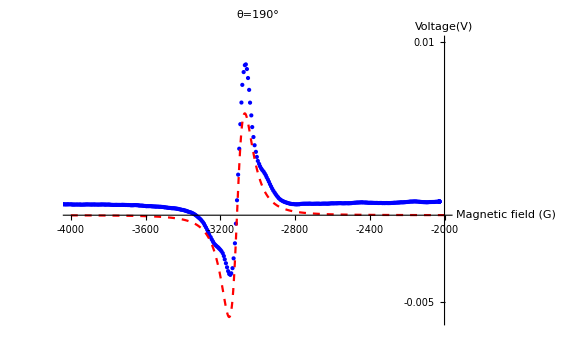

```mathematica
pl190=Show[pa19,  fita190a, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

```mathematica
(*gaussian*)


FindFit[a190 ,-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,{{a,-3120},{v,-100},{s,50}},x]
```

{a→-3113.43,v→-72.2414,s→55.1559}

```mathematica
a2hnin=NonlinearModelFit[a190, {-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,55<s<62 ,-75<v<-64},{{a,-3120},v,s} ,x ]


a2hnin["AdjustedRSquared"]


a2hnin["ParameterTable"]

a2hnin["BestFit"]
```

FittedModel[0.000167914 ⅇ^(-0.000163529 (3113.47+x)^2) (3113.47+x)]

0.705796

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-1655.18] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3113.47 | 1.57444 | -1977.51 | 0.
v | -71.161 | 3.91219 | -18.1895 | 1.04072×10^-52
s | 55.2953 | 1.56986 | 35.2232 | 6.66678×10^-118

0.000167914 ⅇ^(-0.000163529 (3113.47+x)^2) (3113.47+x)

```mathematica
FindMinimum[0.00016791432906125193 ⅇ^(-0.0001635285900071454 (3113.4732889336774+x)^2) (3113.4732889336774+x),{x,-3120}]


FindMaximum[0.00016791432906125193 ⅇ^(-0.0001635285900071454 (3113.4732889336774+x)^2) (3113.4732889336774+x),{x,-3000}]
```

{-0.00563156,{x→-3168.77}}

{0.00563156,{x→-3058.18}}

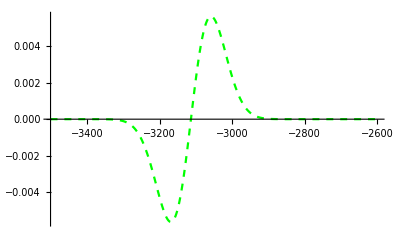

```mathematica
fita190b=Plot[0.00016791432906125193 ⅇ^(-0.0001635285900071454 (3113.4732889336774+x)^2) (3113.4732889336774+x),{x,-3500,-2600}, PlotStyle->{Green, Dashed}, PlotRange->{ {0.007,-0.007}}]
```

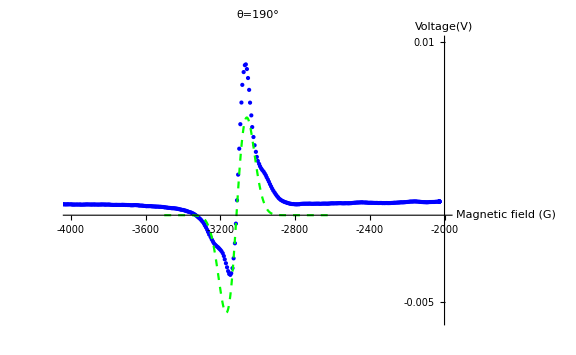

```mathematica
pg190=Show[pa19,  fita190b, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

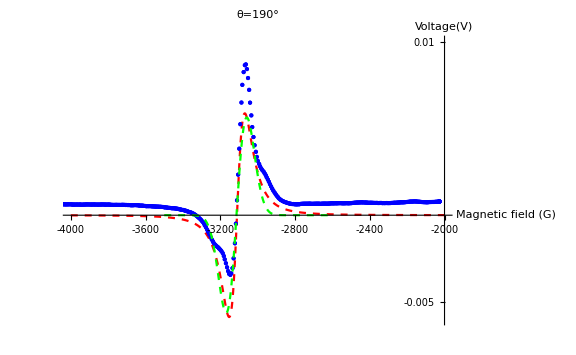

```mathematica
Show[pl190, pg190,ImageSize->Large, AspectRatio->1/GoldenRatio]
```

```mathematica
200 Degrees
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
th=Import["C:\\Users\\Peggy\\Desktop\\M2.6 ectron Spin Resonance\\EPRdata\\crystal\\200", "Table"];
```

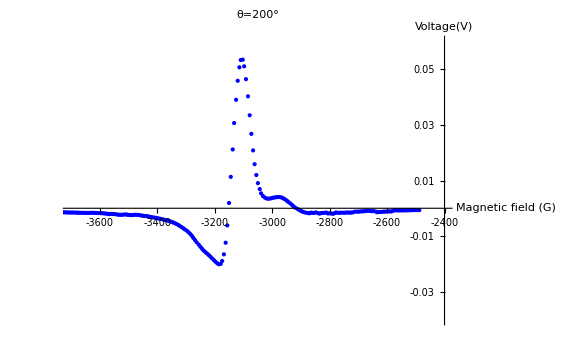

```mathematica
a200=Take[th, {5,270}];
pa20=ListPlot[a200,PlotRange->{{-3700,-2400}, {0.06,-0.04}} ,LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"θ=200°" ,   AxesLabel->{"Magnetic field (G)", " Voltage(V)"}, PlotStyle->Directive[Thin,PointSize[Small],Blue], Ticks-> {{-3600,-3400,-3200,-3000,-2800,-2600,-2400},{-0.03,-0.01,0.01,0.03,0.05}}]
```

```mathematica
FindFit[a200,  -(v*g (-a+x))/(π (g^2/4+(-a+x)^2)^2),{{a,-3160},g,v},x]
```

{a→-3150.41,g→-129.176,v→705.122}

```mathematica
a1th=NonlinearModelFit[a200, { -(v*g (-a+x))/(π (g^2/4+(-a+x)^2)^2),125<g<135, -850<v<-650},{{a,-3150},v,g } ,x ]


a1th["AdjustedRSquared"]

a1th["ParameterTable"]

a1th["BestFit"]
```

FittedModel[(28960.1 (3150.41+x))/((4168.11+(«19»+x)^2)^2)]

0.841048

| Estimate | Standard Error | t-Statistic | P-Value
a | -3150.41 | 1.00145 | -3145.85 | 0.
v | -704.612 | 37.6134 | -18.733 | 2.50445×10^-50
g | 129.122 | 3.96796 | 32.5411 | 3.34779×10^-94

(28960.1 (3150.41+x))/((4168.11+(3150.41+x)^2)^2)

```mathematica
Solve[D[(28960.073554128023 (3150.4087257968235+x))/((4168.112259604353+(3150.4087257968235+x)^2)^2),x]==0,x]
```

{{x→-3187.68},{x→-3113.13}}

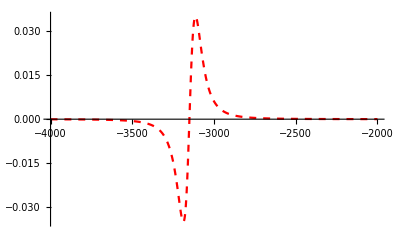

```mathematica
fita200a=Plot[(28960.073554128023 (3150.4087257968235+x))/((4168.112259604353+(3150.4087257968235+x)^2)^2),{x,-4000,-2000}, PlotStyle->{Red, Dashed}, PlotRange->{ {0.047,-0.042}}]
```

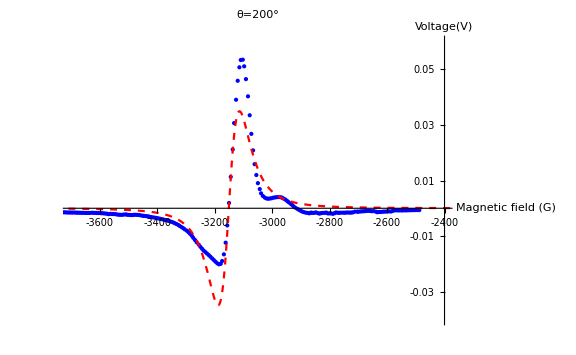

```mathematica
pl200=Show[pa20,  fita200a, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

```mathematica
(*gaussian*)


FindFit[a200 ,-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,{{a,-3200},{v,-400},{s,40}},x]
```

{a→-3152.83,v→-327.067,s→47.0649}

```mathematica
a2th=NonlinearModelFit[a200, {-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,45<s<50 ,-350<v<-324},{{a,-3120},v,s} ,x ]


a2th["AdjustedRSquared"]


a2th["ParameterTable"]

a2th["BestFit"]
```

FittedModel[0.00125108 ⅇ^(-0.000225385 (3152.85+x)^2) (3152.85+x)]

0.826605

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-1368.54] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3152.85 | 1.08098 | -2916.66 | 0.
v | -327.672 | 14.5185 | -22.5693 | 1.8025×10^-63
s | 47.1001 | 1.07457 | 43.8314 | 6.70742×10^-123

0.00125108 ⅇ^(-0.000225385 (3152.85+x)^2) (3152.85+x)

```mathematica
FindMinimum[0.0012510752670322203 ⅇ^(-0.0002253854797560389 (3152.8450362333797+x)^2) (3152.8450362333797+x),{x,-3150}]


FindMaximum[0.0012510752670322203 ⅇ^(-0.0002253854797560389 (3152.8450362333797+x)^2) (3152.8450362333797+x),{x,-3000}]
```

{-0.0357403,{x→-3199.95}}

{0.0357403,{x→-3105.74}}

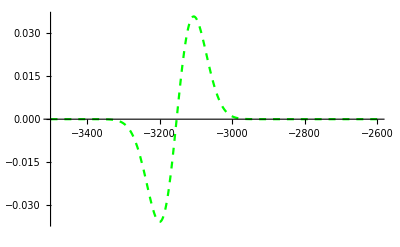

```mathematica
fita200b=Plot[0.0012510752670322203 ⅇ^(-0.0002253854797560389 (3152.8450362333797+x)^2) (3152.8450362333797+x),{x,-3500,-2600}, PlotStyle->{Green, Dashed}, PlotRange->{ {0.047,-0.042}}]
```

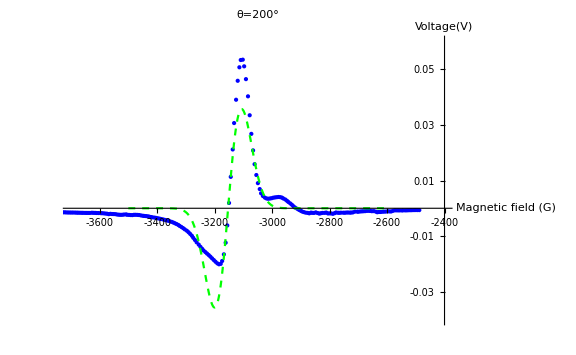

```mathematica
pg200=Show[pa20,  fita200b, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

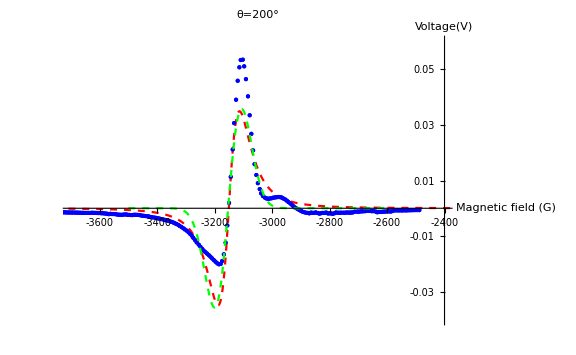

```mathematica
Show[pl200, pg200,ImageSize->Large, AspectRatio->1/GoldenRatio]
```

```mathematica
210 Degrees
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
thten=Import["C:\\Users\\Peggy\\Desktop\\M2.6 ectron Spin Resonance\\EPRdata\\crystal\\210", "Table"];
```

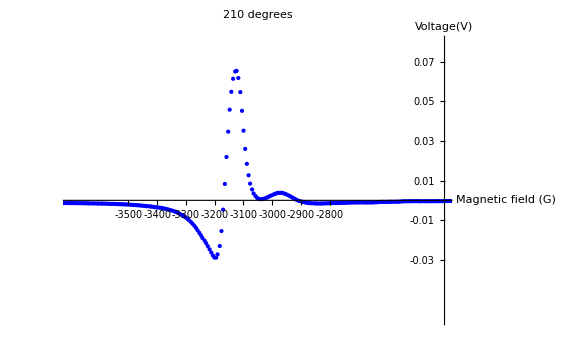

```mathematica
a210=Take[thten, {5,293}];
pa21=ListPlot[a210,PlotRange->{{-3700,-2400}, {0.08,-0.06}} ,LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"210 degrees" ,   AxesLabel->{"Magnetic field (G)", " Voltage(V)"}, PlotStyle->Directive[Thin,PointSize[Small],Blue], Ticks-> {{-3500,-3400,-3300,-3200,-3100,-3000,-2900,-2800},{-0.03,-0.01,0.01,0.03,0.05,0.07}}]
```

```mathematica
FindFit[a210, -(v*g (-a+x))/(π (g^2/4+(-a+x)^2)^2),{{a,-3200},g,v},x]
```

{a→-3166.69,g→-54.177,v→1279.16}

```mathematica
a1thten=NonlinearModelFit[a210, { -(v*g (-a+x))/(π (g^2/4+(-a+x)^2)^2),60<g<70, -2250<v<-250},{{a,-3171},v,g } ,x ]


a1thten["AdjustedRSquared"]

a1thten["ParameterTable"]

a1thten["BestFit"]
```

FittedModel[(28366.7 (3167.84+x))/((3601.96+(«17»+x)^2)^2)]

0.851725

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-1545.94] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3167.84 | 0.850549 | -3724.47 | 0.
v | -1484.87 | 72.8533 | -20.3817 | 1.18084×10^-57
g | 60.0163 | 1.6997 | 35.31 | 2.84332×10^-106

(28366.7 (3167.84+x))/((3601.96+(3167.84+x)^2)^2)

```mathematica
Solve[D[(19499.351605290056 (3160.0530374615046+x))/((3651.2278806200543+(3160.0530374615046+x)^2)^2),x]==0,x]
```

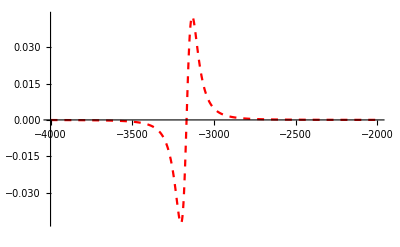

```mathematica
fita210a=Plot[(28366.716459167987 (3167.84187577164+x))/((3601.960232032482+(3167.84187577164+x)^2)^2),{x,-4000,-2000}, PlotStyle->{Red, Dashed}, PlotRange->{ {0.047,-0.042}}]
```

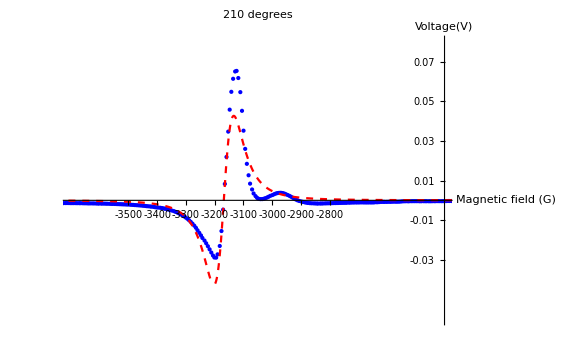

```mathematica
pl210=Show[pa21,  fita210a, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

```mathematica
(*gaussian*)


FindFit[a210 ,-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,{{a,-3200},{v,-400},{s,50}},x]
```

{a→-3168.28,v→-298.826,s→39.5426}

```mathematica
a2thten=NonlinearModelFit[a210, {-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,40<s<60 ,-900<v<-64},{{a,-3170},v,s} ,x ]


a2thten["AdjustedRSquared"]


a2thten["ParameterTable"]

a2thten["BestFit"]
```

FittedModel[0.00189154 ⅇ^(-0.00031174 (3168.5+x)^2) (3168.5+x)]

0.854438

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-1565.67] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3168.5 | 0.793995 | -3990.58 | 0.
v | -304.559 | 11.6798 | -26.0758 | 1.4485×10^-77
s | 40.0487 | 0.791236 | 50.6154 | 9.10019×10^-145

0.00189154 ⅇ^(-0.00031174 (3168.5+x)^2) (3168.5+x)

```mathematica
FindMinimum[0.00029529810484167575 ⅇ^(-0.00004999847351269028 (3160.5012207090645+x)^2) (3160.5012207090645+x),{x,-3100}]


FindMaximum[0.00029529810484167575 ⅇ^(-0.00004999847351269028 (3160.5012207090645+x)^2) (3160.5012207090645+x),{x,-3000}]
```

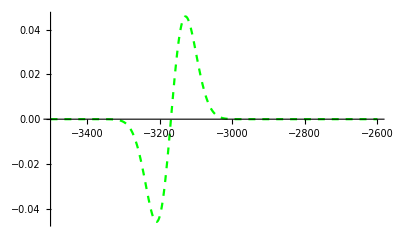

```mathematica
fita210b=Plot[0.0018915382627805418 ⅇ^(-0.00031173986708824675 (3168.5035194817838+x)^2) (3168.5035194817838+x),{x,-3500,-2600}, PlotStyle->{Green, Dashed}, PlotRange->{ {0.047,-0.062}}]
```

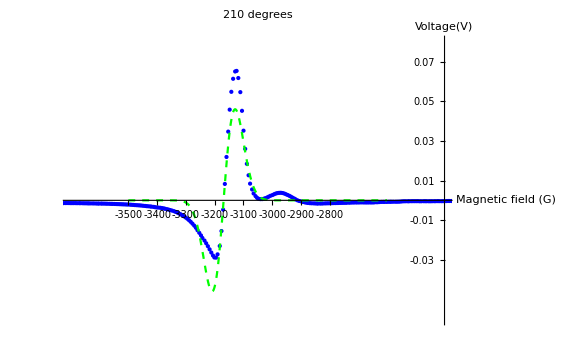

```mathematica
pg210=Show[pa21,  fita210b, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

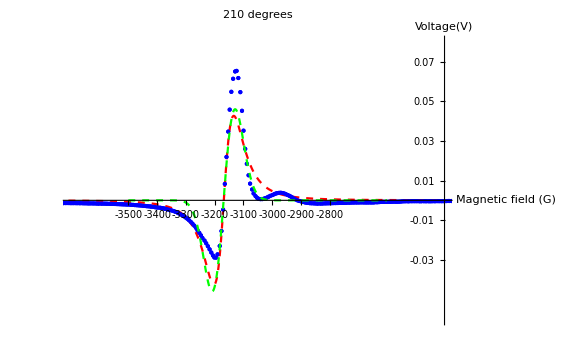

```mathematica
Show[pl210, pg210,ImageSize->Large, AspectRatio->1/GoldenRatio]
```

```mathematica
220 Degrees
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
thtw=Import["C:\\Users\\Peggy\\Desktop\\M2.6 ectron Spin Resonance\\EPRdata\\crystal\\220", "Table"];
```

```mathematica
Length[%72]
```

421

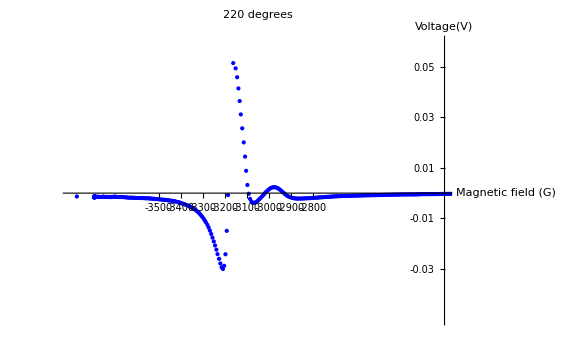

```mathematica
a220=Take[thtw, {5,421}];
pa22=ListPlot[a220,PlotRange->{{-3900,-2200}, {0.06,-0.05}} ,LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"220 degrees" ,   AxesLabel->{"Magnetic field (G)", " Voltage(V)"}, PlotStyle->Directive[Thin,PointSize[Small],Blue], Ticks-> {{-3500,-3400,-3300,-3200,-3100,-3000,-2900,-2800},{-0.03,-0.01,0.01,0.03,0.05,0.07}}]
```

```mathematica
FindFit[a220, -(v * g (-a+x))/(π (g^2+(-a+x)^2)^2),{{a,-3200},g,v},x]
```

{a→-3190.05,g→-39.3393,v→749.241}

```mathematica
a1thtw=NonlinearModelFit[a220, {(-v *g (-a+x))/(π (g^2+(-a+x)^2)^2),30<g<70, -2250<v<-250},{{a,-3200},v,g } ,x ]


a1thtw["AdjustedRSquared"]

a1thtw["ParameterTable"]

a1thtw["BestFit"]
```

FittedModel[(9382.76 (3190.05+x))/((1547.67+(«19»+x)^2)^2)]

0.692794

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-2264.83] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3190.05 | 0.665036 | -4796.81 | 0.
v | -749.274 | 44.3758 | -16.8847 | 4.85926×10^-49
g | 39.3405 | 1.39747 | 28.1512 | 3.36886×10^-98

(9382.76 (3190.05+x))/((1547.67+(3190.05+x)^2)^2)

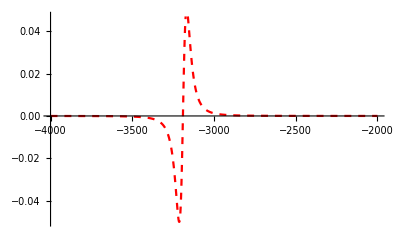

```mathematica
fita220a=Plot[(9382.758965858086 (3190.0524093684703+x))/((1547.6723663983212+(3190.0524093684703+x)^2)^2),{x,-4000,-2000}, PlotStyle->{Red, Dashed}, PlotRange->{ {0.047,-0.052}}]
```

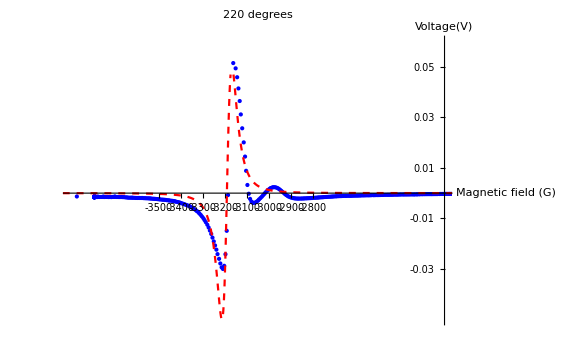

```mathematica
pl220=Show[pa22,  fita220a, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

```mathematica
(*gaussian*)


FindFit[a220 ,-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,{{a,-3200},{v,-400},{s,50}},x]
```

{a→-3190.94,v→-209.107,s→33.5484}

```mathematica
a2thtw=NonlinearModelFit[a220, {-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,30<s<60 ,-900<v<-64},{{a,-3200},v,s} ,x ]


a2thtw["AdjustedRSquared"]


a2thtw["ParameterTable"]

a2thtw["BestFit"]
```

FittedModel[0.00220898 ⅇ^(-0.000444156 (3190.94+x)^2) (3190.94+x)]

0.643832

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-2120.75] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3190.94 | 0.942138 | -3386.92 | 0.
v | -209.138 | 10.9878 | -19.0336 | 1.74922×10^-58
s | 33.5519 | 0.960103 | 34.9462 | 1.45974×10^-125

0.00220898 ⅇ^(-0.000444156 (3190.94+x)^2) (3190.94+x)

```mathematica
FindMinimum[0.00029529810484167575 ⅇ^(-0.00004999847351269028 (3160.5012207090645+x)^2) (3160.5012207090645+x),{x,-3100}]


FindMaximum[0.00029529810484167575 ⅇ^(-0.00004999847351269028 (3160.5012207090645+x)^2) (3160.5012207090645+x),{x,-3000}]
```

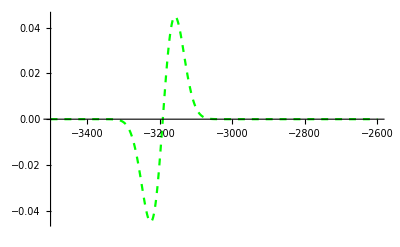

```mathematica
fita220b=Plot[0.002208982978027981 ⅇ^(-0.0004441561541230306 (3190.9440687890733+x)^2) (3190.9440687890733+x),{x,-3500,-2600}, PlotStyle->{Green, Dashed}, PlotRange->{ {0.047,-0.062}}]
```

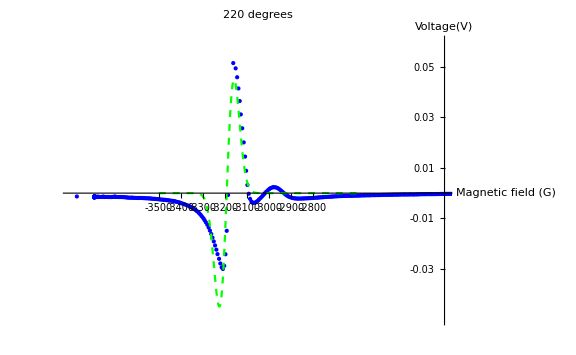

```mathematica
pg220=Show[pa22,  fita220b, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

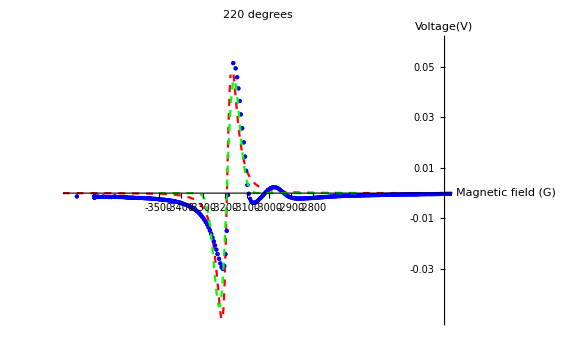

```mathematica
Show[pl220, pg220,ImageSize->Large, AspectRatio->1/GoldenRatio]
```

```mathematica
240 Degrees
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
thf=Import["C:\\Users\\Peggy\\Desktop\\M2.6 ectron Spin Resonance\\EPRdata\\crystal\\240", "Table"];
```

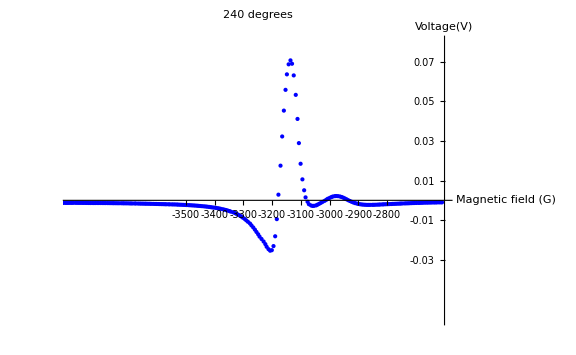

```mathematica
a240=Take[thf, {5,253}];
pa24=ListPlot[a240,PlotRange->{{-3900,-2600}, {0.08,-0.06}} ,LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"240 degrees" ,   AxesLabel->{"Magnetic field (G)", " Voltage(V)"}, PlotStyle->Directive[Thin,PointSize[Small],Blue], Ticks-> {{-3500,-3400,-3300,-3200,-3100,-3000,-2900,-2800},{-0.03,-0.01,0.01,0.03,0.05,0.07}}]
```

```mathematica
FindFit[a240, -(v * g (-a+x))/(π (g^2+(-a+x)^2)^2),{{a,-3200},g,v},x]
```

{a→-3176.65,g→-51.1489,v→1150.38}

```mathematica
a1thf=NonlinearModelFit[a240, {(-v *g (-a+x))/(π (g^2+(-a+x)^2)^2),30<g<70, -2250<v<-250},{{a,-3200},v,g } ,x ]


a1thf["AdjustedRSquared"]

a1thf["ParameterTable"]

a1thf["BestFit"]
```

FittedModel[(18728.1 (3176.64+x))/((2616.06+(«19»+x)^2)^2)]

0.78774

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-1312.37] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3176.64 | 0.988263 | -3214.37 | 0.
v | -1150.32 | 76.0746 | -15.1209 | 5.68396×10^-37
g | 51.1475 | 1.93935 | 26.3734 | 1.18292×10^-73

(18728.1 (3176.64+x))/((2616.06+(3176.64+x)^2)^2)

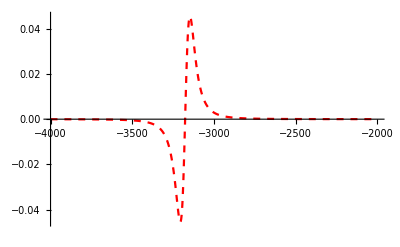

```mathematica
fita240a=Plot[(18728.061887217355 (3176.6449399138846+x))/((2616.064593324989+(3176.6449399138846+x)^2)^2),{x,-4000,-2000}, PlotStyle->{Red, Dashed}, PlotRange->{ {0.047,-0.062}}]
```

```mathematica
pl240=Show[pa24,  fita240a, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

-Graphics-

```mathematica
(*gaussian*)


FindFit[a240 ,-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,{{a,-3200},{v,-400},{s,50}},x]
```

{a→-3178.11,v→-274.385,s→37.4419}

```mathematica
a2thtf=NonlinearModelFit[a240, {-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,30<s<60 ,-900<v<-64},{{a,-3200},v,s} ,x ]


a2thtf["AdjustedRSquared"]


a2thtf["ParameterTable"]

a2thtf["BestFit"]
```

FittedModel[0.00208542 ⅇ^(-0.000356653 (3178.11+x)^2) (3178.11+x)]

0.806303

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-1320.57] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3178.11 | 0.956296 | -3323.36 | 0.
v | -274.39 | 13.5108 | -20.3089 | 1.63312×10^-54
s | 37.4422 | 0.944037 | 39.6618 | 7.26313×10^-109

0.00208542 ⅇ^(-0.000356653 (3178.11+x)^2) (3178.11+x)

```mathematica
fita240b=Plot[0.0020854150832959125 ⅇ^(-0.0003566532929779482 (3178.1132726761016+x)^2) (3178.1132726761016+x),{x,-3500,-2600}, PlotStyle->{Green, Dashed}, PlotRange->{ {0.047,-0.062}}]
```

-Graphics-

```mathematica
pg240=Show[pa24,  fita240b, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

-Graphics-

```mathematica
Show[pl240, pg240,ImageSize->Large, AspectRatio->1/GoldenRatio]
```

-Graphics-

```mathematica
250 Degrees
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
thfi=Import["C:\\Users\\Peggy\\Desktop\\M2.6 ectron Spin Resonance\\EPRdata\\crystal\\250", "Table"];
```

```mathematica
a250=Take[thfi, {5,416}];
pa25=ListPlot[a250,PlotRange->{{-3600,-2600}, {0.05,-0.03}} ,LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"250 degrees" ,   AxesLabel->{"Magnetic field (G)", " Voltage(V)"}, PlotStyle->Directive[Thin,PointSize[Small],Blue], Ticks-> {{-3500,-3400,-3300,-3200,-3100,-3000,-2900,-2800},{-0.03,-0.01,0.01,0.03,0.05,0.07}}]
```

-Graphics-

```mathematica
FindFit[a250, -(v * g (-a+x))/(π (g^2+(-a+x)^2)^2),{{a,-3200},g,v},x]
```

{a→-3160.06,g→-60.4504,v→1014.55}

```mathematica
a1thfi=NonlinearModelFit[a250, {(-v *g (-a+x))/(π (g^2+(-a+x)^2)^2),30<g<70, -2250<v<-250},{{a,-3200},v,g } ,x ]


a1thfi["AdjustedRSquared"]

a1thfi["ParameterTable"]

a1thfi["BestFit"]
```

FittedModel[(19499.4 (3160.05+x))/((3651.23+(«19»+x)^2)^2)]

0.816916

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-2157.24] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3160.05 | 0.806522 | -3918.13 | 0.
v | -1013.8 | 47.1239 | -21.5134 | 3.24959×10^-69
g | 60.4254 | 1.62788 | 37.119 | 4.99924×10^-133

(19499.4 (3160.05+x))/((3651.23+(3160.05+x)^2)^2)

```mathematica
fita250a=Plot[(19499.351605290056 (3160.0530374615046+x))/((3651.2278806200543+(3160.0530374615046+x)^2)^2),{x,-4000,-2000}, PlotStyle->{Red, Dashed}, PlotRange->{ {0.047,-0.062}}]
```

-Graphics-

```mathematica
pl250=Show[pa25,  fita250a, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

```mathematica
FindPeaks[a250]
```

```mathematica
(*gaussian*)


FindFit[a250 ,-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,{{a,-3200},{v,-400},{s,50}},x]
```

{a→-3161.95,v→-235.518,s→43.9202}

```mathematica
a2thtfi=NonlinearModelFit[a250, {-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,30<s<60 ,-900<v<-64},{{a,-3200},v,s} ,x ]


a2thtfi["AdjustedRSquared"]


a2thtfi["ParameterTable"]

a2thtfi["BestFit"]
```

FittedModel[0.00110917 ⅇ^(-0.000259244 (3161.95+x)^2) (3161.95+x)]

0.815105

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-2142.22] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3161.95 | 0.837191 | -3776.85 | 0.
v | -235.494 | 8.71438 | -27.0237 | 5.11001×10^-93
s | 43.9168 | 0.842665 | 52.1166 | 1.05392×10^-182

0.00110917 ⅇ^(-0.000259244 (3161.95+x)^2) (3161.95+x)

```mathematica
fita250b=Plot[0.001109168161630178 ⅇ^(-0.00025924354179679925 (3161.9459538382257+x)^2) (3161.9459538382257+x),{x,-3500,-2600}, PlotStyle->{Green, Dashed}, PlotRange->{ {0.047,-0.062}}]
```

-Graphics-

```mathematica
pg250=Show[pa25,  fita250b, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

-Graphics-

```mathematica
Show[pl250, pg250,ImageSize->Large, AspectRatio->1/GoldenRatio]
```

-Graphics-

```mathematica
260 Degrees
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
thsi=Import["C:\\Users\\Peggy\\Desktop\\M2.6 ectron Spin Resonance\\EPRdata\\crystal\\260", "Table"];
```

```mathematica
a260=Take[thsi, {5,299}];
pa26=ListPlot[a260,PlotRange->{{-3600,-2600}, {0.04,-0.025}} ,LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"260 degrees" ,   AxesLabel->{"Magnetic field (G)", " Voltage(V)"}, PlotStyle->Directive[Thin,PointSize[Small],Blue], Ticks-> {{-3500,-3400,-3300,-3200,-3100,-3000,-2900,-2800},{-0.03,-0.01,0.01,0.03,0.05,0.07}}]
```

-Graphics-

```mathematica
FindFit[a260, -(v * g (-a+x))/(π (g^2+(-a+x)^2)^2),{{a,-3200},g,v},x]
```

{a→-3140.78,g→-74.7929,v→1066.26}

```mathematica
a1thsi=NonlinearModelFit[a260, {(-v *g (-a+x))/(π (g^2+(-a+x)^2)^2),30<g<70, -2250<v<-250},{{a,-3200},v,g } ,x ]


a1thsi["AdjustedRSquared"]

a1thsi["ParameterTable"]

a1thsi["BestFit"]
```

FittedModel[(21450.1 (3139.53+x))/((4897.54+(«19»+x)^2)^2)]

0.804649

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-1478.53] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3139.53 | 1.1741 | -2673.97 | 0.
v | -962.921 | 55.3647 | -17.3923 | 5.42812×10^-47
g | 69.9824 | 2.30881 | 30.311 | 3.53174×10^-92

(21450.1 (3139.53+x))/((4897.54+(3139.53+x)^2)^2)

```mathematica
fita260a=Plot[(21450.10208128035 (3139.5262585579926+x))/((4897.535654638638+(3139.5262585579926+x)^2)^2),{x,-4000,-2000}, PlotStyle->{Red, Dashed}, PlotRange->{ {0.047,-0.062}}]
```

-Graphics-

```mathematica
pl260=Show[pa26,  fita260a, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

-Graphics-

```mathematica
(*gaussian*)


FindFit[a260 ,-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,{{a,-3200},{v,-400},{s,50}},x]
```

{a→-3144.76,v→-258.059,s→55.9513}

```mathematica
a2thtsi=NonlinearModelFit[a260, {-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,30<s<60 ,-900<v<-64},{{a,-3200},v,s} ,x ]


a2thtsi["AdjustedRSquared"]


a2thtsi["ParameterTable"]

a2thtsi["BestFit"]
```

FittedModel[0.00058835 ⅇ^(-0.000159903 (3144.75+x)^2) (3144.75+x)]

0.797161

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-1440.13] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3144.75 | 1.34135 | -2344.46 | 0.
v | -257.866 | 11.9828 | -21.5196 | 3.40422×10^-62
s | 55.9186 | 1.33895 | 41.763 | 3.64676×10^-125

0.00058835 ⅇ^(-0.000159903 (3144.75+x)^2) (3144.75+x)

```mathematica
fita260b=Plot[0.0005883495378206459 ⅇ^(-0.0001599034184836863 (3144.746852256705+x)^2) (3144.746852256705+x),{x,-3500,-2600}, PlotStyle->{Green, Dashed}, PlotRange->{ {0.047,-0.062}}]
```

-Graphics-

```mathematica
pg260=Show[pa26,  fita260b, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

-Graphics-

```mathematica
Show[pl260, pg260,ImageSize->Large, AspectRatio->1/GoldenRatio]
```

-Graphics-

```mathematica
270 Degrees
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
thse=Import["C:\\Users\\Peggy\\Desktop\\M2.6 ectron Spin Resonance\\EPRdata\\crystal\\270", "Table"];
```

```mathematica
a270=Take[thse, {5,338}];
pa27=ListPlot[a270,PlotRange->{{-3600,-2600}, {0.03,-0.02}} ,LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"270 degrees" ,   AxesLabel->{"Magnetic field (G)", " Voltage(V)"}, PlotStyle->Directive[Thin,PointSize[Small],Blue], Ticks-> {{-3500,-3400,-3300,-3200,-3100,-3000,-2900,-2800},{-0.02,-0.01,0.01,0.02,0.03}}]
```

-Graphics-

```mathematica
FindFit[a270, -(v * g (-a+x))/(π (g^2+(-a+x)^2)^2),{{a,-3200},g,v},x]
```

{a→-3120.01,g→88.8438,v→-1203.86}

```mathematica
a1thse=NonlinearModelFit[a270, {(-v *g (-a+x))/(π (g^2+(-a+x)^2)^2),30<g<70, -2250<v<-250},{{a,-3200},v,g } ,x ]


a1thse["AdjustedRSquared"]

a1thse["ParameterTable"]

a1thse["BestFit"]
```

FittedModel[(18442.6 (3114.55+x))/((4900.+(3114.55+x)^2)^2)]

0.731515

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-1608.79] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3114.55 | 1.33892 | -2326.17 | 0.
v | -827.702 | 54.8183 | -15.099 | 1.48587×10^-39
g | 70. | 2.67821 | 26.1369 | 1.77623×10^-82

(18442.6 (3114.55+x))/((4900.+(3114.55+x)^2)^2)

```mathematica
fita270a=Plot[(18442.60539446151 (3114.545464020411+x))/((4900.+(3114.545464020411+x)^2)^2),{x,-4000,-2000}, PlotStyle->{Red, Dashed}, PlotRange->{ {0.047,-0.062}}]
```

-Graphics-

```mathematica
pl270=Show[pa27,  fita270a, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

-Graphics-

```mathematica
(*gaussian*)


FindFit[a270 ,-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,{{a,-3200},{v,-400},{s,50}},x]
```

{a→-3127.18,v→-318.261,s→70.0628}

```mathematica
a2thtse=NonlinearModelFit[a270, {-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,30<s<60 ,-900<v<-64},{{a,-3200},v,s} ,x ]


a2thtse["AdjustedRSquared"]


a2thtse["ParameterTable"]

a2thtse["BestFit"]
```

FittedModel[0.0004614 ⅇ^(-0.000138924 (3121.39+x)^2) (3121.39+x)]

0.75061

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-1562.14] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3121.39 | 1.54496 | -2020.37 | 0.
v | -249.721 | 12.4436 | -20.0682 | 3.59819×10^-59
s | 59.9924 | 1.54224 | 38.8994 | 1.68308×10^-125

0.0004614 ⅇ^(-0.000138924 (3121.39+x)^2) (3121.39+x)

```mathematica
fita270b=Plot[0.00046139950146255565 ⅇ^(-0.0001389242820525798 (3121.390538069715+x)^2) (3121.390538069715+x),{x,-3500,-2600}, PlotStyle->{Green, Dashed}, PlotRange->{ {0.047,-0.062}}]
```

-Graphics-

```mathematica
pg270=Show[pa27,  fita270b, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

-Graphics-

```mathematica
Show[pl270, pg270,ImageSize->Large, AspectRatio->1/GoldenRatio]
```

-Graphics-

```mathematica
280 Degrees
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
thei=Import["C:\\Users\\Peggy\\Desktop\\M2.6 ectron Spin Resonance\\EPRdata\\crystal\\280", "Table"];
```

```mathematica
a280=Take[thei, {5,311}];
pa28=ListPlot[a280,PlotRange->{{-3600,-2600}, {0.03,-0.015}} ,LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"280 degrees" ,   AxesLabel->{"Magnetic field (G)", " Voltage(V)"}, PlotStyle->Directive[Thin,PointSize[Small],Blue], Ticks-> {{-3500,-3400,-3300,-3200,-3100,-3000,-2900,-2800},{-0.02,-0.01,0.01,0.02,0.03}}]
```

-Graphics-

```mathematica
FindFit[a280, -(v * g (-a+x))/(π (g^2+(-a+x)^2)^2),{{a,-3150},g,v},x]
```

{a→-3096.57,g→-99.1848,v→1200.25}

```mathematica
a1the=NonlinearModelFit[a280, {(-v *g (-a+x))/(π (g^2+(-a+x)^2)^2),80<g<100, -2250<v<-250},{{a,-3150},v,g } ,x ]


a1the["AdjustedRSquared"]

a1the["ParameterTable"]

a1the["BestFit"]
```

FittedModel[(36921.7 (3096.22+x))/((9635.58+(«18»+x)^2)^2)]

0.704197

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-1352.65] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3096.22 | 2.09622 | -1477.05 | 0.
v | -1181.66 | 87.3149 | -13.5333 | 5.52356×10^-33
g | 98.161 | 4.18255 | 23.4691 | 3.22189×10^-70

(36921.7 (3096.22+x))/((9635.58+(3096.22+x)^2)^2)

```mathematica
fita280a=Plot[(36921.691840145606 (3096.218753470498+x))/((9635.580570730095+(3096.218753470498+x)^2)^2),{x,-4000,-2000}, PlotStyle->{Red, Dashed}, PlotRange->{ {0.047,-0.062}}]
```

-Graphics-

```mathematica
pl280=Show[pa28,  fita280a, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

-Graphics-

```mathematica
(*gaussian*)


FindFit[a280 ,-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,{{a,-3200},{v,-400},{s,50}},x]
```

{a→-3106.69,v→-328.607,s→79.5073}

```mathematica
a2the=NonlinearModelFit[a280, {-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,30<s<60 ,-900<v<-64},{{a,-3200},v,s} ,x ]


a2the["AdjustedRSquared"]


a2the["ParameterTable"]

a2the["BestFit"]
```

FittedModel[0.000386462 ⅇ^(-0.00013892 (3092.92+x)^2) (3092.92+x)]

0.684201

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-1382.89] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3092.92 | 1.89571 | -1631.53 | 0.
v | -209.173 | 12.7995 | -16.3423 | 1.59757×10^-43
s | 59.9934 | 1.89451 | 31.667 | 2.8204×10^-98

0.000386462 ⅇ^(-0.00013892 (3092.92+x)^2) (3092.92+x)

```mathematica
fita280b=Plot[0.0003864618665913144 ⅇ^(-0.00013891967378757143 (3092.91807704076+x)^2) (3092.91807704076+x),{x,-3500,-2600}, PlotStyle->{Green, Dashed}, PlotRange->{ {0.047,-0.062}}]
```

-Graphics-

```mathematica
pg280=Show[pa28,  fita280b, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

-Graphics-

```mathematica
Show[pl280, pg280,ImageSize->Large, AspectRatio->1/GoldenRatio]
```

-Graphics-

```mathematica
290 Degrees
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
thn=Import["C:\\Users\\Peggy\\Desktop\\M2.6 ectron Spin Resonance\\EPRdata\\crystal\\290", "Table"];
```

```mathematica
a290=Take[thn, {5,286}];
pa29=ListPlot[a290,PlotRange->{{-3600,-2600}, {0.03,-0.015}} ,LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"290 degrees" ,   AxesLabel->{"Magnetic field (G)", " Voltage(V)"}, PlotStyle->Directive[Thin,PointSize[Small],Blue], Ticks-> {{-3500,-3400,-3300,-3200,-3100,-3000,-2900,-2800},{-0.02,-0.01,0.01,0.02,0.03}}]
```

-Graphics-

```mathematica
FindFit[a290, -(v * g (-a+x))/(π (g^2+(-a+x)^2)^2),{{a,-3100},g,v},x]
```

{a→-3072.7,g→-102.72,v→1017.32}

```mathematica
a1thn=NonlinearModelFit[a290, {(-v *g (-a+x))/(π (g^2+(-a+x)^2)^2),90<g<110, -2250<v<-250},{{a,-3100},v,g } ,x ]


a1thn["AdjustedRSquared"]

a1thn["ParameterTable"]

a1thn["BestFit"]
```

FittedModel[(32801.6 (3072.5+x))/((10434.6+(«18»+x)^2)^2)]

0.684909

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-1216.62] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3072.5 | 2.37497 | -1293.7 | 0.
v | -1008.8 | 81.3882 | -12.3949 | 2.10707×10^-28
g | 102.15 | 4.7585 | 21.4668 | 4.99967×10^-61

(32801.6 (3072.5+x))/((10434.6+(3072.5+x)^2)^2)

```mathematica
fita290a=Plot[(32801.55891922222 (3072.499902610075+x))/((10434.614246562849+(3072.499902610075+x)^2)^2),{x,-4000,-2000}, PlotStyle->{Red, Dashed}, PlotRange->{ {0.047,-0.062}}]
```

-Graphics-

```mathematica
pl290=Show[pa29,  fita290a, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

-Graphics-

```mathematica
(*gaussian*)


FindFit[a290 ,-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,{{a,-3100},{v,-400},{s,50}},x]
```

{a→-3083.99,v→-279.158,s→82.6607}

```mathematica
a2thn=NonlinearModelFit[a290, {-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,70<s<90 ,-300<v<-64},{{a,-3100},v,s} ,x ]


a2thn["AdjustedRSquared"]


a2thn["ParameterTable"]

a2thn["BestFit"]
```

FittedModel[0.000198519 ⅇ^(-0.0000741336 (3083.59+x)^2) (3083.59+x)]

0.701983

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-1192.04] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3083.59 | 2.60314 | -1184.57 | 0.
v | -275.628 | 16.9312 | -16.2792 | 2.38525×10^-42
s | 82.1254 | 2.60593 | 31.5148 | 6.44498×10^-94

0.000198519 ⅇ^(-0.0000741336 (3083.59+x)^2) (3083.59+x)

```mathematica
fita290b=Plot[0.0001985185273342785 ⅇ^(-0.00007413364900699049 (3083.5938478489725+x)^2) (3083.5938478489725+x),{x,-3500,-2600}, PlotStyle->{Green, Dashed}, PlotRange->{ {0.047,-0.062}}]
```

-Graphics-

```mathematica
pg290=Show[pa29,  fita290b, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

-Graphics-

```mathematica
Show[pl290, pg290,ImageSize->Large, AspectRatio->1/GoldenRatio]
```

-Graphics-

```mathematica
300 Degrees
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
trh=Import["C:\\Users\\Peggy\\Desktop\\M2.6 ectron Spin Resonance\\EPRdata\\crystal\\300", "Table"];
```

```mathematica
a300=Take[trh, {5,278}];
pa30=ListPlot[a300,PlotRange->{{-3600,-2600}, {0.02,-0.01}} ,LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"300 degrees" ,   AxesLabel->{"Magnetic field (G)", " Voltage(V)"}, PlotStyle->Directive[Thin,PointSize[Small],Blue], Ticks-> {{-3500,-3400,-3300,-3200,-3100,-3000,-2900,-2800},{-0.02,-0.01,0.01,0.02,0.03}}]
```

-Graphics-

```mathematica
FindFit[a300, -(v * g (-a+x))/(π (g^2+(-a+x)^2)^2),{{a,-3100},g,v},x]
```

{a→-3051.61,g→102.429,v→-795.786}

```mathematica
a1trh=NonlinearModelFit[a300, {(-v *g (-a+x))/(π (g^2+(-a+x)^2)^2),100<g<110, -850<v<-650},{{a,-3070},v,g } ,x ]


a1trh["AdjustedRSquared"]

a1trh["ParameterTable"]

a1trh["BestFit"]
```

FittedModel[(25563.4 (3051.46+x))/((10399.3+(«18»+x)^2)^2)]

0.681321

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-1177.49] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3051.46 | 2.43174 | -1254.85 | 0.
v | -787.529 | 65.1506 | -12.0878 | 3.40848×10^-27
g | 101.977 | 4.88267 | 20.8855 | 2.20315×10^-58

(25563.4 (3051.46+x))/((10399.3+(3051.46+x)^2)^2)

```mathematica
fita300a=Plot[(25563.44018569231 (3051.461368061698+x))/((10399.322064313694+(3051.461368061698+x)^2)^2),{x,-4000,-2000}, PlotStyle->{Red, Dashed}, PlotRange->{ {0.047,-0.062}}]
```

-Graphics-

```mathematica
pl300=Show[pa30,  fita300a, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

-Graphics-

```mathematica
(*gaussian*)


FindFit[a300 ,-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,{{a,-3070},{v,-400},{s,50}},x]
```

{a→-3061.87,v→-213.33,s→81.7538}

```mathematica
a2trh=NonlinearModelFit[a300, {-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,70<s<90 ,-300<v<-64},{{a,-3100},v,s} ,x ]


a2trh["AdjustedRSquared"]


a2trh["ParameterTable"]

a2trh["BestFit"]
```

FittedModel[0.000155177 ⅇ^(-0.0000744435 (3062.02+x)^2) (3062.02+x)]

0.684385

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-1145.88] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3062.02 | 2.74203 | -1116.7 | 0.
v | -214.108 | 13.8599 | -15.448 | 4.79661×10^-39
s | 81.9543 | 2.74356 | 29.8715 | 1.01875×10^-87

0.000155177 ⅇ^(-0.0000744435 (3062.02+x)^2) (3062.02+x)

```mathematica
fita300b=Plot[0.00015517732638930436 ⅇ^(-0.00007444351151289224 (3062.020692672506+x)^2) (3062.020692672506+x),{x,-3500,-2600}, PlotStyle->{Green, Dashed}, PlotRange->{ {0.047,-0.062}}]
```

-Graphics-

```mathematica
pg300=Show[pa30,  fita300b, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

-Graphics-

```mathematica
Show[pl300, pg300,ImageSize->Large, AspectRatio->1/GoldenRatio]
```

-Graphics-

```mathematica
310 Degrees
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
trte=Import["C:\\Users\\Peggy\\Desktop\\M2.6 ectron Spin Resonance\\EPRdata\\crystal\\310", "Table"];
```

```mathematica
a310=Take[trte, {5,278}];
pa31=ListPlot[a310,PlotRange->{{-3600,-2600}, {0.015,-0.01}} ,LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"310 degrees" ,   AxesLabel->{"Magnetic field (G)", " Voltage(V)"}, PlotStyle->Directive[Thin,PointSize[Small],Blue], Ticks-> {{-3500,-3400,-3300,-3200,-3100,-3000,-2900,-2800},{-0.02,-0.01,0.01,0.02,0.03}}]
```

-Graphics-

```mathematica
FindFit[a310, -(v * g (-a+x))/(π (g^2+(-a+x)^2)^2),{{a,-3100},g,v},x]
```

{a→-3038.61,g→-101.239,v→659.357}

```mathematica
a1trt=NonlinearModelFit[a310, {(-v *g (-a+x))/(π (g^2+(-a+x)^2)^2),90<g<110, -750<v<-600},{{a,-3070},v,g } ,x ]


a1trt["AdjustedRSquared"]

a1trt["ParameterTable"]

a1trt["BestFit"]
```

FittedModel[(20899.4 (3038.4+x))/((10119.+(«18»+x)^2)^2)]

0.69614

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-1188.64] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3038.4 | 2.32364 | -1307.6 | 0.
v | -652.701 | 52.1089 | -12.5257 | 1.05084×10^-28
g | 100.593 | 4.62278 | 21.7604 | 2.04603×10^-61

(20899.4 (3038.4+x))/((10119.+(3038.4+x)^2)^2)

```mathematica
fita310a=Plot[(20899.43016244421 (3038.400043100065+x))/((10119.04308665117+(3038.400043100065+x)^2)^2),{x,-4000,-2000}, PlotStyle->{Red, Dashed}, PlotRange->{ {0.047,-0.062}}]
```

-Graphics-

```mathematica
pl310=Show[pa31,  fita310a, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

-Graphics-

```mathematica
(*gaussian*)


FindFit[a310 ,-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,{{a,-3070},{v,-400},{s,50}},x]
```

{a→-3045.66,v→-165.425,s→77.6069}

```mathematica
a2trte=NonlinearModelFit[a310, {-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,70<s<80 ,-300<v<-64},{{a,-3070},v,s} ,x ]


a2trte["AdjustedRSquared"]


a2trte["ParameterTable"]

a2trte["BestFit"]
```

FittedModel[0.000142854 ⅇ^(-0.0000843592 (3045.21+x)^2) (3045.21+x)]

0.68815

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-1163.8] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3045.21 | 2.55249 | -1193.03 | 0.
v | -163.395 | 10.5064 | -15.552 | 2.03503×10^-39
s | 76.9873 | 2.55209 | 30.1664 | 1.31249×10^-88

0.000142854 ⅇ^(-0.0000843592 (3045.21+x)^2) (3045.21+x)

```mathematica
fita310b=Plot[0.0001428543512379 ⅇ^(-0.00008435916561301877 (3045.213180771305+x)^2) (3045.213180771305+x),{x,-3500,-2600}, PlotStyle->{Green, Dashed}, PlotRange->{ {0.047,-0.062}}]
```

-Graphics-

```mathematica
pg310=Show[pa31,  fita310b, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

-Graphics-

```mathematica
Show[pl310, pg310,ImageSize->Large, AspectRatio->1/GoldenRatio]
```

-Graphics-

```mathematica
320 Degrees
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
trtw=Import["C:\\Users\\Peggy\\Desktop\\M2.6 ectron Spin Resonance\\EPRdata\\crystal\\320", "Table"];
```

```mathematica
a320=Take[trtw, {5,286}];
pa32=ListPlot[a320,PlotRange->{{-3600,-2600}, {0.02,-0.01}} ,LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"320 degrees" ,   AxesLabel->{"Magnetic field (G)", " Voltage(V)"}, PlotStyle->Directive[Thin,PointSize[Small],Blue], Ticks-> {{-3500,-3400,-3300,-3200,-3100,-3000,-2900,-2800},{-0.02,-0.01,0.01,0.02,0.03}}]
```

-Graphics-

```mathematica
FindFit[a320, -(v * g (-a+x))/(π (g^2+(-a+x)^2)^2),{{a,-3070},g,v},x]
```

{a→-3036.94,g→-97.2469,v→737.311}

```mathematica
a1trw=NonlinearModelFit[a320, {(-v *g (-a+x))/(π (g^2+(-a+x)^2)^2),90<g<110, -750<v<-600},{{a,-3070},v,g } ,x ]


a1trw["AdjustedRSquared"]

a1trw["ParameterTable"]

a1trw["BestFit"]
```

FittedModel[(21617.9 (3036.34+x))/((9101.67+(«18»+x)^2)^2)]

0.684579

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-1231.2] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3036.34 | 2.22747 | -1363.14 | 0.
v | -711.872 | 57.7831 | -12.3197 | 3.85668×10^-28
g | 95.4027 | 4.46882 | 21.3485 | 1.30641×10^-60

(21617.9 (3036.34+x))/((9101.67+(3036.34+x)^2)^2)

```mathematica
fita320a=Plot[(21617.87360349977 (3036.337438890301+x))/((9101.674727885447+(3036.337438890301+x)^2)^2),{x,-4000,-2000}, PlotStyle->{Red, Dashed}, PlotRange->{ {0.047,-0.062}}]
```

-Graphics-

```mathematica
pl320=Show[pa32,  fita320a, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

-Graphics-

```mathematica
(*gaussian*)


FindFit[a320 ,-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,{{a,-3070},{v,-400},{s,50}},x]
```

{a→-3042.56,v→-180.146,s→73.1635}

```mathematica
a2trtw=NonlinearModelFit[a320, {-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,70<s<80 ,-300<v<-64},{{a,-3070},v,s} ,x ]


a2trtw["AdjustedRSquared"]


a2trtw["ParameterTable"]

a2trtw["BestFit"]
```

FittedModel[0.000183022 ⅇ^(-0.0000930779 (3042.65+x)^2) (3042.65+x)]

0.679996

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-1207.28] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3042.65 | 2.432 | -1251.09 | 0.
v | -180.625 | 11.6304 | -15.5305 | 1.26036×10^-39
s | 73.2928 | 2.4356 | 30.0924 | 1.37284×10^-89

0.000183022 ⅇ^(-0.0000930779 (3042.65+x)^2) (3042.65+x)

```mathematica
fita320b=Plot[0.0001830216172861681 ⅇ^(-0.0000930779486703212 (3042.65147591729+x)^2) (3042.65147591729+x),{x,-3500,-2600}, PlotStyle->{Green, Dashed}, PlotRange->{ {0.047,-0.062}}]
```

-Graphics-

```mathematica
pg320=Show[pa32,  fita320b, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

-Graphics-

```mathematica
Show[pl320, pg320,ImageSize->Large, AspectRatio->1/GoldenRatio]
```

-Graphics-

```mathematica
330 Degrees
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
trth=Import["C:\\Users\\Peggy\\Desktop\\M2.6 ectron Spin Resonance\\EPRdata\\crystal\\330", "Table"];
```

```mathematica
a330=Take[trth, {5,810}];
pa33=ListPlot[a330,PlotRange->{{-3600,-2600}, {0.02,-0.01}} ,LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"330 degrees" ,   AxesLabel->{"Magnetic field (G)", " Voltage(V)"}, PlotStyle->Directive[Thin,PointSize[Small],Blue], Ticks-> {{-3500,-3400,-3300,-3200,-3100,-3000,-2900,-2800},{-0.02,-0.01,0.01,0.02,0.03}}]
```

-Graphics-

```mathematica
FindFit[a330, -(v * g (-a+x))/(π (g^2+(-a+x)^2)^2),{{a,-3060},g,v},x]
```

{a→-3039.5,g→-91.057,v→767.205}

```mathematica
a1trth=NonlinearModelFit[a330, {(-v *g (-a+x))/(π (g^2+(-a+x)^2)^2),90<g<110, -750<v<-600},{{a,-3060},v,g } ,x ]


a1trth["AdjustedRSquared"]

a1trth["ParameterTable"]

a1trth["BestFit"]
```

FittedModel[(21389.6 (3039.29+x))/((8173.5+(«19»+x)^2)^2)]

0.682058

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-3558.71] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3039.29 | 1.2814 | -2371.85 | 0.
v | -743.272 | 36.4821 | -20.3736 | 1.06193×10^-74
g | 90.4074 | 2.56028 | 35.3115 | 1.37798×10^-165

(21389.6 (3039.29+x))/((8173.5+(3039.29+x)^2)^2)

```mathematica
fita330a=Plot[(21389.56084348005 (3039.2936001564626+x))/((8173.499309388676+(3039.2936001564626+x)^2)^2),{x,-4000,-2000}, PlotStyle->{Red, Dashed}, PlotRange->{ {0.047,-0.062}}]
```

-Graphics-

```mathematica
pl330=Show[pa33,  fita330a, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

-Graphics-

```mathematica
(*gaussian*)


FindFit[a330 ,-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,{{a,-3070},{v,-400},{s,50}},x]
```

{a→-3042.75,v→-178.61,s→66.3722}

```mathematica
a2trth=NonlinearModelFit[a330, {-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,70<s<80 ,-300<v<-64},{{a,-3070},v,s} ,x ]


a2trth["AdjustedRSquared"]


a2trth["ParameterTable"]

a2trth["BestFit"]
```

FittedModel[0.000221347 ⅇ^(-0.0000999218 (3045.78+x)^2) (3045.78+x)]

0.675652

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-3484.21] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3045.78 | 1.40899 | -2161.68 | 0.
v | -196.394 | 7.58404 | -25.8957 | 5.75345×10^-108
s | 70.7384 | 1.40932 | 50.1931 | 7.80613×10^-250

0.000221347 ⅇ^(-0.0000999218 (3045.78+x)^2) (3045.78+x)

```mathematica
fita330b=Plot[0.0002213473002016498 ⅇ^(-0.0000999217510995667 (3045.776735090195+x)^2) (3045.776735090195+x),{x,-3500,-2600}, PlotStyle->{Green, Dashed}, PlotRange->{ {0.047,-0.062}}]
```

-Graphics-

```mathematica
pg330=Show[pa33,  fita330b, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

-Graphics-

```mathematica
Show[pl330, pg330,ImageSize->Large, AspectRatio->1/GoldenRatio]
```

-Graphics-

```mathematica
340 Degrees
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
trtfo=Import["C:\\Users\\Peggy\\Desktop\\M2.6 ectron Spin Resonance\\EPRdata\\crystal\\340", "Table"];
```

```mathematica
a340=Take[trtfo, {5,481}];
pa34=ListPlot[a340,PlotRange->{{-3600,-2600}, {0.025,-0.015}} ,LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"340 degrees" ,   AxesLabel->{"Magnetic field (G)", " Voltage(V)"}, PlotStyle->Directive[Thin,PointSize[Small],Blue], Ticks-> {{-3500,-3400,-3300,-3200,-3100,-3000,-2900,-2800},{-0.02,-0.01,0.01,0.02,0.03}}]
```

-Graphics-

```mathematica
FindFit[a340, -(v * g (-a+x))/(π (g^2+(-a+x)^2)^2),{{a,-3060},g,v},x]
```

{a→-3051.56,g→-86.1771,v→870.059}

```mathematica
a1trfo=NonlinearModelFit[a340, {(-v *g (-a+x))/(π (g^2+(-a+x)^2)^2),90<g<110, -750<v<-600},{{a,-3060},v,g } ,x ]


a1trfo["AdjustedRSquared"]

a1trfo["ParameterTable"]

a1trfo["BestFit"]
```

FittedModel[(21475.1 (3052.74+x))/((8104.27+(«18»+x)^2)^2)]

0.663038

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-2004.62] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3052.74 | 2.05675 | -1484.25 | 0.
v | -749.425 | 59.2189 | -12.6552 | 7.9324×10^-32
g | 90.0237 | 4.09426 | 21.9878 | 2.21234×10^-74

(21475.1 (3052.74+x))/((8104.27+(3052.74+x)^2)^2)

```mathematica
fita340a=Plot[(21475.09562661276 (3052.743328214915+x))/((8104.266373249808+(3052.743328214915+x)^2)^2),{x,-4000,-2000}, PlotStyle->{Red, Dashed}, PlotRange->{ {0.047,-0.062}}]
```

-Graphics-

```mathematica
pl340=Show[pa34,  fita340a, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

-Graphics-

```mathematica
(*gaussian*)


FindFit[a340 ,-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,{{a,-3070},{v,-400},{s,50}},x]
```

{a→-3054.52,v→-205.493,s→63.1534}

```mathematica
a2trfo=NonlinearModelFit[a340, {-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,70<s<80 ,-300<v<-64},{{a,-3070},v,s} ,x ]


a2trfo["AdjustedRSquared"]


a2trfo["ParameterTable"]

a2trfo["BestFit"]
```

FittedModel[0.000277512 ⅇ^(-0.000101826 (3059.21+x)^2) (3059.21+x)]

0.686624

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-2079.64] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3059.21 | 1.75933 | -1738.85 | 0.
v | -239.354 | 11.6597 | -20.5282 | 1.80699×10^-67
s | 70.0739 | 1.76196 | 39.7704 | 4.06834×10^-153

0.000277512 ⅇ^(-0.000101826 (3059.21+x)^2) (3059.21+x)

```mathematica
fita340b=Plot[0.0002775117501379451 ⅇ^(-0.00010182564628618514 (3059.210708096264+x)^2) (3059.210708096264+x),{x,-3500,-2600}, PlotStyle->{Green, Dashed}, PlotRange->{ {0.047,-0.062}}]
```

-Graphics-

```mathematica
pg340=Show[pa34,  fita340b, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

-Graphics-

```mathematica
Show[pl340, pg340,ImageSize->Large, AspectRatio->1/GoldenRatio]
```

-Graphics-

```mathematica
350 Degrees
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
trtfi=Import["C:\\Users\\Peggy\\Desktop\\M2.6 ectron Spin Resonance\\EPRdata\\crystal\\350", "Table"];
```

```mathematica
a350=Take[trtfi, {5,265}];
pa35=ListPlot[a350,PlotRange->{{-3600,-2600}, {0.03,-0.015}} ,LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"350 degrees" ,   AxesLabel->{"Magnetic field (G)", " Voltage(V)"}, PlotStyle->Directive[Thin,PointSize[Small],Blue], Ticks-> {{-3500,-3400,-3300,-3200,-3100,-3000,-2900,-2800},{-0.02,-0.01,0.01,0.02,0.03}}]
```

-Graphics-

```mathematica
FindFit[a350, -(v * g (-a+x))/(π (g^2+(-a+x)^2)^2),{{a,-3100},g,v},x]
```

{a→-3071.22,g→82.5953,v→-1003.69}

```mathematica
a1trfi=NonlinearModelFit[a350, {(-v *g (-a+x))/(π (g^2+(-a+x)^2)^2),90<g<110, -1050<v<-600},{{a,-3100},v,g } ,x ]


a1trfi["AdjustedRSquared"]

a1trfi["ParameterTable"]

a1trfi["BestFit"]
```

FittedModel[(30063.4 (3073.57+x))/((8102.38+(«18»+x)^2)^2)]

0.690448

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-1140.7] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3073.57 | 2.32683 | -1320.92 | 0.
v | -1049.26 | 94.0875 | -11.1519 | 7.86011×10^-24
g | 90.0132 | 4.66302 | 19.3037 | 5.4543×10^-52

(30063.4 (3073.57+x))/((8102.38+(3073.57+x)^2)^2)

```mathematica
fita350a=Plot[(30063.38337831237 (3073.569178031443+x))/((8102.38124373501+(3073.569178031443+x)^2)^2),{x,-4000,-2000}, PlotStyle->{Red, Dashed}, PlotRange->{ {0.047,-0.062}}]
```

-Graphics-

```mathematica
pl350=Show[pa35,  fita350a, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

-Graphics-

```mathematica
(*gaussian*)


FindFit[a350 ,-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,{{a,-3100},{v,-400},{s,50}},x]
```

{a→-3075.92,v→-252.034,s→63.0757}

```mathematica
a2trfi=NonlinearModelFit[a350, {-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,70<s<80 ,-300<v<-64},{{a,-3100},v,s} ,x ]


a2trfi["AdjustedRSquared"]


a2trfi["ParameterTable"]

a2trfi["BestFit"]
```

FittedModel[0.000339932 ⅇ^(-0.000101915 (3080.77+x)^2) (3080.77+x)]

0.696912

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-1139.55] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3080.77 | 2.34274 | -1315.03 | 0.
v | -292.806 | 18.9629 | -15.441 | 1.53812×10^-38
s | 70.0432 | 2.34006 | 29.9322 | 6.72222×10^-86

0.000339932 ⅇ^(-0.000101915 (3080.77+x)^2) (3080.77+x)

```mathematica
fita350b=Plot[0.0003399322265276514 ⅇ^(-0.00010191502446473346 (3080.772618258949+x)^2) (3080.772618258949+x),{x,-4000,-2000},  PlotStyle->{Green, Dashed}, PlotRange->{ {0.047,-0.062}}]
```

-Graphics-

```mathematica
pg350=Show[pa35,  fita350b, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

-Graphics-

```mathematica
Show[pl350, pg350,ImageSize->Large, AspectRatio->1/GoldenRatio]
```

-Graphics-

```mathematica
360 Degrees
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
trts=Import["C:\\Users\\Peggy\\Desktop\\M2.6 ectron Spin Resonance\\EPRdata\\crystal\\360.0000", "Table"];
```

```mathematica
a360=Take[trts, {5,574}];
pa36=ListPlot[a360,PlotRange->{{-3600,-2600}, {0.05,-0.025}} ,LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"360 degrees" ,   AxesLabel->{"Magnetic field (G)", " Voltage(V)"}, PlotStyle->Directive[Thin,PointSize[Small],Blue], Ticks-> {{-3500,-3400,-3300,-3200,-3100,-3000,-2900,-2800},{-0.02,-0.01,0.01,0.02,0.03,0.04,0.05}}]
```

-Graphics-

```mathematica
FindFit[a360, -(v * g (-a+x))/(π (g^2+(-a+x)^2)^2),{{a,-3200},g,v},x]
```

{a→-3106.11,g→81.115,v→-1463.56}

```mathematica
a1trs=NonlinearModelFit[a360, {(-v *g (-a+x))/(π (g^2+(-a+x)^2)^2),80<g<90, -1600<v<-900},{{a,-3200},v,g } ,x ]


a1trs["AdjustedRSquared"]

a1trs["ParameterTable"]

a1trs["BestFit"]
```

FittedModel[(37843.1 (3106.13+x))/((6587.6+(«17»+x)^2)^2)]

0.629576

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-2534.9] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3106.13 | 1.50123 | -2069.05 | 0.
v | -1464.78 | 93.9299 | -15.5944 | 6.94225×10^-46
g | 81.164 | 3.003 | 27.0277 | 5.30088×10^-104

(37843.1 (3106.13+x))/((6587.6+(3106.13+x)^2)^2)

```mathematica
fita360a=Plot[(37843.1368168342 (3106.12753393788+x))/((6587.599384993876+(3106.12753393788+x)^2)^2),{x,-4000,-2000}, PlotStyle->{Red, Dashed}, PlotRange->{ {0.047,-0.062}}]
```

-Graphics-

```mathematica
pl360=Show[pa36,  fita360a, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

-Graphics-

```mathematica
(*gaussian*)


FindFit[a360 ,-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,{{a,-3200},{v,-1400},{s,80}},x]
```

{a→-3115.11,v→-415.202,s→66.4475}

```mathematica
a2trsi=NonlinearModelFit[a360, {-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,65<s<80 ,-500<v<-204},{{a,-3200},v,s} ,x ]


a2trsi["AdjustedRSquared"]


a2trsi["ParameterTable"]

a2trsi["BestFit"]
```

FittedModel[0.000563784 ⅇ^(-0.000113031 (3115.15+x)^2) (3115.15+x)]

0.653591

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-2482.] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3115.15 | 1.65286 | -1884.71 | 0.
v | -415.778 | 20.0244 | -20.7636 | 1.19627×10^-71
s | 66.5099 | 1.65206 | 40.2588 | 2.18926×10^-168

0.000563784 ⅇ^(-0.000113031 (3115.15+x)^2) (3115.15+x)

```mathematica
fita360b=Plot[0.0005637842966040307 ⅇ^(-0.00011303094899171425 (3115.153562722057+x)^2) (3115.153562722057+x),{x,-4000,-2000},  PlotStyle->{Green, Dashed}, PlotRange->{ {0.047,-0.062}}]
```

-Graphics-

```mathematica
pg360=Show[pa36,  fita360b, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

-Graphics-

```mathematica
Show[pl360, pg360,ImageSize->Large, AspectRatio->1/GoldenRatio]
```

-Graphics-

```mathematica
0 degree
```

```mathematica
zero=Import["C:\\Users\\Peggy\\Desktop\\M2.6 ectron Spin Resonance\\EPRdata\\crystal\\test1", "Table"];
```

```mathematica
a0=Take[zero, {5,4329}];
pa0=ListPlot[a0,PlotRange->{{-4000,-2300}, {0.02,-0.015}} ,LabelStyle->{10,GrayLevel[0],Bold},ImageSize->Large, AspectRatio->1/GoldenRatio, PlotLabel->"0 degrees" ,   AxesLabel->{"Magnetic field (G)", " Voltage(V)"}, PlotStyle->Directive[Thin,PointSize[Small],Blue]]
```

-Graphics-

```mathematica
FindFit[a0, -(v * g (-a+x))/(π (g^2+(-a+x)^2)^2),{{a,-3150},{v,-5000},{g,50 }},x]
```

{a→-3091.85,v→-692.961,g→84.4356}

```mathematica
al0=NonlinearModelFit[a0, {(-v *g (-a+x))/(π (g^2+(-a+x)^2)^2),80<g<90, -1600<v<-900},{{a,-3150},v,g } ,x ]
```

FittedModel[(25783.8 (3093.+x))/((8097.82+(«18»+x)^2)^2)]

```mathematica
al0["AdjustedRSquared"]
```

0.574913

```mathematica
al0["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-19105.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-861.023] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1947.73] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3093. | 0.566552 | -5459.34 | 0.
v | -900.145 | 19.6235 | -45.8708 | 0.
g | 89.9879 | 1.13357 | 79.3847 | 0.

```mathematica
al0["BestFit"]
```

(25783.8 (3093.+x))/((8097.82+(3093.+x)^2)^2)

```mathematica
fital0=Plot[(25783.7913564444 (3093.001368954273+x))/((8097.823446958351+(3093.001368954273+x)^2)^2),{x,-4000,-2000}, PlotStyle->{Red, Dashed}, PlotRange->{ {0.047,-0.032}}]
```

-Graphics-

```mathematica
pl0=Show[pa0,  fital0, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

-Graphics-

```mathematica
(*gaussian*)
```

```mathematica
FindFit[a0,-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,{{a,-3200},{v,-1400},{s,80}},x]
```

{a→-3095.35,v→-161.262,s→62.5293}

```mathematica
ag0=NonlinearModelFit[a0, {-(ⅇ^(-(-a+x)^2/(2 s^2)) (-a+x))/(√(2 π) (s^2)^(3/2))v,50<s<70, -200<v<-0.4},{{a,-3100},v,s} ,x ]
```

FittedModel[0.000264059 ⅇ^(-0.000128296 (3095.32+x)^2) (3095.32+x)]

```mathematica
ag0["AdjustedRSquared"]
```

0.56319

```mathematica
ag0["ParameterTable"]

ag0["BestFit"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-18291.6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-900.484] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2332.65] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
a | -3095.32 | 0.684431 | -4522.47 | 0.
v | -161.037 | 3.41591 | -47.1433 | 0.
s | 62.4279 | 0.682244 | 91.5038 | 0.

0.000264059 ⅇ^(-0.000128296 (3095.32+x)^2) (3095.32+x)

```mathematica
fitag0=Plot[0.0002640588236945857 ⅇ^(-0.00012829581139877467 (3095.3195740362758+x)^2) (3095.3195740362758+x),{x,-4000,-2000}, PlotStyle->{Green, Dashed}, PlotRange->{ {0.047,-0.032}}]
```

-Graphics-

```mathematica
pg0=Show[pa0,  fitag0, PlotStyle->{Red, Dashed, Thick}, ImageSize->Large, AspectRatio->1/GoldenRatio]
```

-Graphics-

```mathematica
Show[pl0,pg0]
```

-Graphics-